# Mathematical Modelling (PX4515, MX4553) Temperature

# Marco Thiel office: Meston Building 332 m.thiel@abdn.ac.uk Office hours: Wednesdays 1pm-2pm (https://us02web.zoom.us/j/268409842) Tel: 01224 27 3160 Feedback link: https://wolfr.am/11MyiKgJu 7 March, 2025

## Shakespearean Networks

This is a text cell.

```mathematica
Manipulate[
Module[{gmap=playNetwork[speechSequences[[i]],n],g},
g=gmap[[2]];
Pane[Labeled[Text@Grid[{{Labeled[GraphPlot[g,MultiedgeStyle->None,ImageSize->{300,200},AspectRatio->2/3],"character networks",Top],Labeled[Grid[Join[{{"character","page rank"}},(List@@@Take[Sort[GraphUtilities`PageRanks[g],#1[[2]]>#2[[2]]&],5])/.{a_,b_}:>{a,NumberForm[b,{6,3}]}],Dividers->All,Background->{{ColorData[33][5],ColorData[33][6]},{ColorData[33][7]}}],"key characters",Top]},{Labeled[Column[GraphUtilities`CommunityStructurePartition[g,Weighted->True]],"communities",Top],SpanFromLeft}},Dividers->All,Background->{{ColorData[33][2]},{},{{1,1}->ColorData[33][3],{1,2}->ColorData[33][4]}}],Text@gmap[[1]],Top],{590,440}]],
{{i,1,""},Dynamic[Thread[Rule[Range[8],Map[StringReplace[#,"The Tragedy of "->""]&,First/@speechSequences]]],SynchronousUpdating->False],ControlType->PopupMenu},{{n,2,"maximum proximity"},Thread[Rule[Range[2,4],Range[1,3]]],ControlType->RadioButton},
AutorunSequencing->{2},
SynchronousInitialization->False,
Initialization:>(
Quiet@Get["GraphUtilities`"];speechSequences={"The Tragedy of Antony and Cleopatra"->{{"PHILO","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","Attendant","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","DEMETRIUS","PHILO","DEMETRIUS"},{"CHARMIAN","ALEXAS","Soothsayer","CHARMIAN","Soothsayer","ALEXAS","DOMITIUS ENOBARBUS","CHARMIAN","Soothsayer","CHARMIAN","Soothsayer","CHARMIAN","IRAS","CHARMIAN","ALEXAS","CHARMIAN","Soothsayer","CHARMIAN","ALEXAS","CHARMIAN","Soothsayer","CHARMIAN","Soothsayer","CHARMIAN","Soothsayer","CHARMIAN","ALEXAS","CHARMIAN","ALEXAS","DOMITIUS ENOBARBUS","IRAS","CHARMIAN","IRAS","CHARMIAN","Soothsayer","IRAS","Soothsayer","IRAS","CHARMIAN","IRAS","CHARMIAN","IRAS","CHARMIAN","ALEXAS","DOMITIUS ENOBARBUS","CHARMIAN","CLEOPATRA","DOMITIUS ENOBARBUS","CLEOPATRA","CHARMIAN","CLEOPATRA","DOMITIUS ENOBARBUS","CLEOPATRA","ALEXAS","CLEOPATRA","Messenger","MARK ANTONY","Messenger","MARK ANTONY","Messenger","MARK ANTONY","Messenger","MARK ANTONY","Messenger","MARK ANTONY","Messenger","MARK ANTONY","First Attendant","Second Attendant","MARK ANTONY","Second Messenger","MARK ANTONY","Second Messenger","MARK ANTONY","DOMITIUS ENOBARBUS","MARK ANTONY","DOMITIUS ENOBARBUS","MARK ANTONY","DOMITIUS ENOBARBUS","MARK ANTONY","DOMITIUS ENOBARBUS","MARK ANTONY","DOMITIUS ENOBARBUS","MARK ANTONY","DOMITIUS ENOBARBUS","MARK ANTONY","DOMITIUS ENOBARBUS","MARK ANTONY","DOMITIUS ENOBARBUS","MARK ANTONY","DOMITIUS ENOBARBUS","MARK ANTONY","DOMITIUS ENOBARBUS"},{"CLEOPATRA","CHARMIAN","CLEOPATRA","CHARMIAN","CLEOPATRA","CHARMIAN","CLEOPATRA","CHARMIAN","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY"},{"OCTAVIUS CAESAR","LEPIDUS","OCTAVIUS CAESAR","LEPIDUS","Messenger","OCTAVIUS CAESAR","Messenger","OCTAVIUS CAESAR","LEPIDUS","OCTAVIUS CAESAR","LEPIDUS","OCTAVIUS CAESAR","LEPIDUS","OCTAVIUS CAESAR"},{"CLEOPATRA","CHARMIAN","CLEOPATRA","CHARMIAN","CLEOPATRA","CHARMIAN","CLEOPATRA","CHARMIAN","CLEOPATRA","MARDIAN","CLEOPATRA","MARDIAN","CLEOPATRA","MARDIAN","CLEOPATRA","ALEXAS","CLEOPATRA","ALEXAS","CLEOPATRA","ALEXAS","CLEOPATRA","ALEXAS","CLEOPATRA","ALEXAS","CLEOPATRA","CHARMIAN","CLEOPATRA","CHARMIAN","CLEOPATRA","CHARMIAN","CLEOPATRA"},{"POMPEY","MENECRATES","POMPEY","MENECRATES","POMPEY","MENAS","POMPEY","MENAS","POMPEY","VARRIUS","POMPEY","MENAS","POMPEY"},{"LEPIDUS","DOMITIUS ENOBARBUS","LEPIDUS","DOMITIUS ENOBARBUS","LEPIDUS","DOMITIUS ENOBARBUS","LEPIDUS","DOMITIUS ENOBARBUS","MARK ANTONY","OCTAVIUS CAESAR","LEPIDUS","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","DOMITIUS ENOBARBUS","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","OCTAVIUS CAESAR","LEPIDUS","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","LEPIDUS","MECAENAS","LEPIDUS","DOMITIUS ENOBARBUS","MARK ANTONY","DOMITIUS ENOBARBUS","MARK ANTONY","DOMITIUS ENOBARBUS","OCTAVIUS CAESAR","AGRIPPA","OCTAVIUS CAESAR","AGRIPPA","OCTAVIUS CAESAR","MARK ANTONY","AGRIPPA","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","OCTAVIUS CAESAR","LEPIDUS","MARK ANTONY","LEPIDUS","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","LEPIDUS","MECAENAS","DOMITIUS ENOBARBUS","AGRIPPA","MECAENAS","DOMITIUS ENOBARBUS","MECAENAS","DOMITIUS ENOBARBUS","MECAENAS","DOMITIUS ENOBARBUS","AGRIPPA","DOMITIUS ENOBARBUS","AGRIPPA","DOMITIUS ENOBARBUS","AGRIPPA","DOMITIUS ENOBARBUS","AGRIPPA","DOMITIUS ENOBARBUS","MECAENAS","DOMITIUS ENOBARBUS","MECAENAS","AGRIPPA","DOMITIUS ENOBARBUS"},{"MARK ANTONY","OCTAVIA","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","Soothsayer","MARK ANTONY","Soothsayer","MARK ANTONY","Soothsayer","MARK ANTONY","Soothsayer","MARK ANTONY"},{"LEPIDUS","AGRIPPA","LEPIDUS","MECAENAS","LEPIDUS","MECAENAS","AGRIPPA","LEPIDUS"},{"CLEOPATRA","Attendants","CLEOPATRA","CHARMIAN","CLEOPATRA","MARDIAN","CLEOPATRA","CHARMIAN","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CHARMIAN","CLEOPATRA","CHARMIAN","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","CHARMIAN","CLEOPATRA","CHARMIAN","CLEOPATRA"},{"POMPEY","OCTAVIUS CAESAR","POMPEY","OCTAVIUS CAESAR","MARK ANTONY","POMPEY","LEPIDUS","OCTAVIUS CAESAR","MARK ANTONY","OCTAVIUS CAESAR","POMPEY","OCTAVIUS CAESAR","MARK ANTONY","LEPIDUS","POMPEY","MARK ANTONY","POMPEY","MARK ANTONY","OCTAVIUS CAESAR","POMPEY","LEPIDUS","POMPEY","OCTAVIUS CAESAR","POMPEY","MARK ANTONY","POMPEY","MARK ANTONY","POMPEY","MARK ANTONY","POMPEY","DOMITIUS ENOBARBUS","POMPEY","DOMITIUS ENOBARBUS","POMPEY","DOMITIUS ENOBARBUS","POMPEY","DOMITIUS ENOBARBUS","POMPEY","OCTAVIUS CAESAR","MARK ANTONY","LEPIDUS","POMPEY","MENAS","DOMITIUS ENOBARBUS","MENAS","DOMITIUS ENOBARBUS","MENAS","DOMITIUS ENOBARBUS","MENAS","DOMITIUS ENOBARBUS","MENAS","DOMITIUS ENOBARBUS","MENAS","DOMITIUS ENOBARBUS","MENAS","DOMITIUS ENOBARBUS","MENAS","DOMITIUS ENOBARBUS","MENAS","DOMITIUS ENOBARBUS","MENAS","DOMITIUS ENOBARBUS","MENAS","DOMITIUS ENOBARBUS","MENAS","DOMITIUS ENOBARBUS","MENAS","DOMITIUS ENOBARBUS","MENAS","DOMITIUS ENOBARBUS","MENAS","DOMITIUS ENOBARBUS","MENAS"},{"First Servant","Second Servant","First Servant","Second Servant","First Servant","Second Servant","First Servant","MARK ANTONY","LEPIDUS","MARK ANTONY","LEPIDUS","MARK ANTONY","POMPEY","LEPIDUS","DOMITIUS ENOBARBUS","LEPIDUS","MENAS","POMPEY","MENAS","POMPEY","LEPIDUS","MARK ANTONY","LEPIDUS","MARK ANTONY","LEPIDUS","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","POMPEY","MENAS","POMPEY","MENAS","POMPEY","MARK ANTONY","MENAS","POMPEY","MENAS","POMPEY","MENAS","POMPEY","MENAS","POMPEY","MENAS","POMPEY","MENAS","POMPEY","MARK ANTONY","DOMITIUS ENOBARBUS","MENAS","POMPEY","DOMITIUS ENOBARBUS","MENAS","DOMITIUS ENOBARBUS","MENAS","DOMITIUS ENOBARBUS","MENAS","POMPEY","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","OCTAVIUS CAESAR","DOMITIUS ENOBARBUS","POMPEY","MARK ANTONY","DOMITIUS ENOBARBUS","OCTAVIUS CAESAR","POMPEY","MARK ANTONY","POMPEY","DOMITIUS ENOBARBUS","MENAS","DOMITIUS ENOBARBUS","MENAS"},{"VENTIDIUS","SILIUS","VENTIDIUS","SILIUS","VENTIDIUS","SILIUS","VENTIDIUS"},{"AGRIPPA","DOMITIUS ENOBARBUS","AGRIPPA","DOMITIUS ENOBARBUS","AGRIPPA","DOMITIUS ENOBARBUS","AGRIPPA","DOMITIUS ENOBARBUS","AGRIPPA","DOMITIUS ENOBARBUS","AGRIPPA","DOMITIUS ENOBARBUS","AGRIPPA","DOMITIUS ENOBARBUS","AGRIPPA","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","OCTAVIUS CAESAR","MARK ANTONY","OCTAVIUS CAESAR","OCTAVIA","MARK ANTONY","OCTAVIA","OCTAVIUS CAESAR","OCTAVIA","MARK ANTONY","DOMITIUS ENOBARBUS","AGRIPPA","DOMITIUS ENOBARBUS","AGRIPPA","DOMITIUS ENOBARBUS","OCTAVIUS CAESAR","MARK ANTONY","OCTAVIUS CAESAR","LEPIDUS","OCTAVIUS CAESAR","MARK ANTONY"},{"CLEOPATRA","ALEXAS","CLEOPATRA","ALEXAS","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","CHARMIAN","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CHARMIAN","CLEOPATRA","CHARMIAN","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","Messenger","CLEOPATRA","CHARMIAN","CLEOPATRA","CHARMIAN","CLEOPATRA","CHARMIAN","CLEOPATRA","CHARMIAN"},{"MARK ANTONY","OCTAVIA","MARK ANTONY","OCTAVIA","MARK ANTONY"},{"DOMITIUS ENOBARBUS","EROS","DOMITIUS ENOBARBUS","EROS","DOMITIUS ENOBARBUS","EROS","DOMITIUS ENOBARBUS","EROS","DOMITIUS ENOBARBUS","EROS","DOMITIUS ENOBARBUS","EROS"},{"OCTAVIUS CAESAR","MECAENAS","OCTAVIUS CAESAR","MECAENAS","AGRIPPA","OCTAVIUS CAESAR","AGRIPPA","OCTAVIUS CAESAR","AGRIPPA","OCTAVIUS CAESAR","MECAENAS","OCTAVIUS CAESAR","OCTAVIA","OCTAVIUS CAESAR","OCTAVIA","OCTAVIUS CAESAR","OCTAVIA","OCTAVIUS CAESAR","OCTAVIA","OCTAVIUS CAESAR","OCTAVIA","OCTAVIUS CAESAR","OCTAVIA","OCTAVIUS CAESAR","AGRIPPA","MECAENAS","OCTAVIA","OCTAVIUS CAESAR"},{"CLEOPATRA","DOMITIUS ENOBARBUS","CLEOPATRA","DOMITIUS ENOBARBUS","CLEOPATRA","DOMITIUS ENOBARBUS","CLEOPATRA","DOMITIUS ENOBARBUS","CLEOPATRA","DOMITIUS ENOBARBUS","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","CANIDIUS","MARK ANTONY","DOMITIUS ENOBARBUS","CANIDIUS","DOMITIUS ENOBARBUS","MARK ANTONY","DOMITIUS ENOBARBUS","MARK ANTONY","CLEOPATRA","MARK ANTONY","Messenger","MARK ANTONY","Soldier","MARK ANTONY","Soldier","CANIDIUS","Soldier","CANIDIUS","Soldier","CANIDIUS","Soldier","CANIDIUS","Messenger","CANIDIUS"},{"OCTAVIUS CAESAR","TAURUS","OCTAVIUS CAESAR"},{"MARK ANTONY"},{"DOMITIUS ENOBARBUS","SCARUS","DOMITIUS ENOBARBUS","SCARUS","DOMITIUS ENOBARBUS","SCARUS","DOMITIUS ENOBARBUS","SCARUS","DOMITIUS ENOBARBUS","CANIDIUS","DOMITIUS ENOBARBUS","CANIDIUS","SCARUS","CANIDIUS","DOMITIUS ENOBARBUS"},{"MARK ANTONY","All","MARK ANTONY","EROS","IRAS","CHARMIAN","CLEOPATRA","MARK ANTONY","EROS","MARK ANTONY","CHARMIAN","IRAS","EROS","MARK ANTONY","CLEOPATRA","EROS","IRAS","CLEOPATRA","EROS","MARK ANTONY","EROS","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY"},{"OCTAVIUS CAESAR","DOLABELLA","OCTAVIUS CAESAR","EUPHRONIUS","OCTAVIUS CAESAR","EUPHRONIUS","OCTAVIUS CAESAR","EUPHRONIUS","OCTAVIUS CAESAR","THYREUS","OCTAVIUS CAESAR","THYREUS"},{"CLEOPATRA","DOMITIUS ENOBARBUS","CLEOPATRA","DOMITIUS ENOBARBUS","CLEOPATRA","MARK ANTONY","EUPHRONIUS","MARK ANTONY","EUPHRONIUS","MARK ANTONY","CLEOPATRA","MARK ANTONY","DOMITIUS ENOBARBUS","Attendant","CLEOPATRA","DOMITIUS ENOBARBUS","CLEOPATRA","THYREUS","CLEOPATRA","THYREUS","DOMITIUS ENOBARBUS","THYREUS","CLEOPATRA","THYREUS","CLEOPATRA","THYREUS","CLEOPATRA","DOMITIUS ENOBARBUS","THYREUS","CLEOPATRA","THYREUS","CLEOPATRA","THYREUS","CLEOPATRA","MARK ANTONY","THYREUS","DOMITIUS ENOBARBUS","MARK ANTONY","DOMITIUS ENOBARBUS","MARK ANTONY","THYREUS","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","First Attendant","MARK ANTONY","First Attendant","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","DOMITIUS ENOBARBUS"},{"OCTAVIUS CAESAR","MECAENAS","OCTAVIUS CAESAR"},{"MARK ANTONY","DOMITIUS ENOBARBUS","MARK ANTONY","DOMITIUS ENOBARBUS","MARK ANTONY","DOMITIUS ENOBARBUS","MARK ANTONY","CLEOPATRA","DOMITIUS ENOBARBUS","MARK ANTONY","All","MARK ANTONY","CLEOPATRA","DOMITIUS ENOBARBUS","MARK ANTONY","DOMITIUS ENOBARBUS","MARK ANTONY"},{"First Soldier","Second Soldier","First Soldier","Second Soldier","First Soldier","Second Soldier","Third Soldier","Fourth Soldier","Third Soldier","Fourth Soldier","First Soldier","Second Soldier","First Soldier","Third Soldier","Fourth Soldier","Third Soldier","First Soldier","Second Soldier","First Soldier","Second Soldier","All","First Soldier","Third Soldier","First Soldier","All"},{"MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","EROS","CLEOPATRA","MARK ANTONY","Soldier","Captain","All","MARK ANTONY","CHARMIAN","CLEOPATRA"},{"Soldier","MARK ANTONY","Soldier","MARK ANTONY","Soldier","MARK ANTONY","Soldier","EROS","MARK ANTONY","Soldier","MARK ANTONY"},{"OCTAVIUS CAESAR","AGRIPPA","OCTAVIUS CAESAR","Messenger","OCTAVIUS CAESAR","DOMITIUS ENOBARBUS","Soldier","DOMITIUS ENOBARBUS","Soldier","DOMITIUS ENOBARBUS"},{"AGRIPPA","SCARUS","MARK ANTONY","SCARUS","MARK ANTONY","SCARUS","EROS","SCARUS","MARK ANTONY","SCARUS"},{"MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY"},{"First Soldier","Second Soldier","DOMITIUS ENOBARBUS","Third Soldier","Second Soldier","DOMITIUS ENOBARBUS","First Soldier","Third Soldier","DOMITIUS ENOBARBUS","Second Soldier","First Soldier","Third Soldier","First Soldier","Second Soldier","Third Soldier","Second Soldier","First Soldier","Third Soldier"},{"MARK ANTONY","SCARUS","MARK ANTONY"},{"OCTAVIUS CAESAR"},{"MARK ANTONY","SCARUS","MARK ANTONY","CLEOPATRA","MARK ANTONY"},{"CLEOPATRA","CHARMIAN","CLEOPATRA"},{"MARK ANTONY","EROS","MARK ANTONY","EROS","MARK ANTONY","EROS","MARK ANTONY","MARDIAN","MARK ANTONY","MARDIAN","MARK ANTONY","MARDIAN","MARK ANTONY","EROS","MARK ANTONY","EROS","MARK ANTONY","EROS","MARK ANTONY","EROS","MARK ANTONY","EROS","MARK ANTONY","EROS","MARK ANTONY","EROS","MARK ANTONY","EROS","MARK ANTONY","EROS","MARK ANTONY","First Guard","MARK ANTONY","Second Guard","First Guard","All","MARK ANTONY","First Guard","Second Guard","Third Guard","DERCETAS","DIOMEDES","DERCETAS","DIOMEDES","MARK ANTONY","DIOMEDES","MARK ANTONY","DIOMEDES","MARK ANTONY","DIOMEDES","MARK ANTONY","DIOMEDES","MARK ANTONY","First Guard","All","MARK ANTONY"},{"CLEOPATRA","CHARMIAN","CLEOPATRA","DIOMEDES","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","All","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","MARK ANTONY","CLEOPATRA","CHARMIAN","IRAS","CHARMIAN","IRAS","CHARMIAN","IRAS","CHARMIAN","CLEOPATRA"},{"OCTAVIUS CAESAR","DOLABELLA","OCTAVIUS CAESAR","DERCETAS","OCTAVIUS CAESAR","DERCETAS","OCTAVIUS CAESAR","DERCETAS","OCTAVIUS CAESAR","AGRIPPA","MECAENAS","AGRIPPA","MECAENAS","OCTAVIUS CAESAR","Egyptian","OCTAVIUS CAESAR","Egyptian","OCTAVIUS CAESAR","PROCULEIUS","OCTAVIUS CAESAR","All","OCTAVIUS CAESAR"},{"CLEOPATRA","PROCULEIUS","CLEOPATRA","PROCULEIUS","CLEOPATRA","PROCULEIUS","CLEOPATRA","PROCULEIUS","GALLUS","IRAS","CHARMIAN","CLEOPATRA","PROCULEIUS","CLEOPATRA","PROCULEIUS","CLEOPATRA","PROCULEIUS","CLEOPATRA","PROCULEIUS","DOLABELLA","PROCULEIUS","CLEOPATRA","DOLABELLA","CLEOPATRA","DOLABELLA","CLEOPATRA","DOLABELLA","CLEOPATRA","DOLABELLA","CLEOPATRA","DOLABELLA","CLEOPATRA","DOLABELLA","CLEOPATRA","DOLABELLA","CLEOPATRA","DOLABELLA","CLEOPATRA","DOLABELLA","CLEOPATRA","DOLABELLA","CLEOPATRA","DOLABELLA","OCTAVIUS CAESAR","DOLABELLA","OCTAVIUS CAESAR","CLEOPATRA","OCTAVIUS CAESAR","CLEOPATRA","OCTAVIUS CAESAR","CLEOPATRA","OCTAVIUS CAESAR","CLEOPATRA","SELEUCUS","CLEOPATRA","SELEUCUS","CLEOPATRA","SELEUCUS","OCTAVIUS CAESAR","CLEOPATRA","OCTAVIUS CAESAR","CLEOPATRA","OCTAVIUS CAESAR","CLEOPATRA","OCTAVIUS CAESAR","CLEOPATRA","OCTAVIUS CAESAR","CLEOPATRA","IRAS","CLEOPATRA","CHARMIAN","DOLABELLA","CHARMIAN","CLEOPATRA","DOLABELLA","CLEOPATRA","DOLABELLA","CLEOPATRA","IRAS","CLEOPATRA","IRAS","CLEOPATRA","IRAS","CLEOPATRA","Guard","CLEOPATRA","Guard","CLEOPATRA","Clown","CLEOPATRA","Clown","CLEOPATRA","Clown","CLEOPATRA","Clown","CLEOPATRA","Clown","CLEOPATRA","Clown","CLEOPATRA","Clown","CLEOPATRA","Clown","CLEOPATRA","CHARMIAN","CLEOPATRA","CHARMIAN","CLEOPATRA","CHARMIAN","CLEOPATRA","CHARMIAN","First Guard","CHARMIAN","First Guard","CHARMIAN","First Guard","Second Guard","First Guard","CHARMIAN","DOLABELLA","Second Guard","DOLABELLA","DOLABELLA","OCTAVIUS CAESAR","DOLABELLA","First Guard","OCTAVIUS CAESAR","First Guard","OCTAVIUS CAESAR","DOLABELLA","First Guard","OCTAVIUS CAESAR"}},"A Midsummer Night's Dream"->{{"THESEUS","HIPPOLYTA","THESEUS","EGEUS","THESEUS","EGEUS","THESEUS","HERMIA","THESEUS","HERMIA","THESEUS","HERMIA","THESEUS","HERMIA","THESEUS","DEMETRIUS","LYSANDER","EGEUS","LYSANDER","THESEUS","EGEUS","LYSANDER","HERMIA","LYSANDER","HERMIA","LYSANDER","HERMIA","LYSANDER","HERMIA","LYSANDER","HERMIA","LYSANDER","HERMIA","LYSANDER","HERMIA","HELENA","HERMIA","HELENA","HERMIA","HELENA","HERMIA","HELENA","HERMIA","HELENA","HERMIA","LYSANDER","HERMIA","LYSANDER","HELENA"},{"QUINCE","BOTTOM","QUINCE","BOTTOM","QUINCE","BOTTOM","QUINCE","BOTTOM","QUINCE","BOTTOM","QUINCE","BOTTOM","QUINCE","FLUTE","QUINCE","FLUTE","QUINCE","FLUTE","QUINCE","BOTTOM","QUINCE","BOTTOM","QUINCE","STARVELING","QUINCE","SNOUT","QUINCE","SNUG","QUINCE","BOTTOM","QUINCE","ALL","BOTTOM","QUINCE","BOTTOM","QUINCE","BOTTOM","QUINCE","BOTTOM","QUINCE","BOTTOM"},{"PUCK","Fairy","PUCK","Fairy","PUCK","Fairy","OBERON","TITANIA","OBERON","TITANIA","OBERON","TITANIA","OBERON","TITANIA","OBERON","TITANIA","OBERON","TITANIA","OBERON","PUCK","OBERON","PUCK","OBERON","DEMETRIUS","HELENA","DEMETRIUS","HELENA","DEMETRIUS","HELENA","DEMETRIUS","HELENA","DEMETRIUS","HELENA","DEMETRIUS","HELENA","OBERON","PUCK","OBERON","PUCK"},{"TITANIA","Fairy","OBERON","LYSANDER","HERMIA","LYSANDER","HERMIA","LYSANDER","HERMIA","LYSANDER","HERMIA","PUCK","HELENA","DEMETRIUS","HELENA","DEMETRIUS","HELENA","LYSANDER","HELENA","LYSANDER","HELENA","LYSANDER","HERMIA"},{"BOTTOM","QUINCE","BOTTOM","QUINCE","BOTTOM","SNOUT","STARVELING","BOTTOM","QUINCE","BOTTOM","SNOUT","STARVELING","BOTTOM","SNOUT","BOTTOM","QUINCE","SNOUT","BOTTOM","QUINCE","BOTTOM","QUINCE","SNOUT","BOTTOM","QUINCE","PUCK","QUINCE","BOTTOM","QUINCE","BOTTOM","PUCK","FLUTE","QUINCE","FLUTE","QUINCE","FLUTE","BOTTOM","QUINCE","PUCK","BOTTOM","SNOUT","BOTTOM","QUINCE","BOTTOM","TITANIA","BOTTOM","TITANIA","BOTTOM","TITANIA","BOTTOM","TITANIA","PEASEBLOSSOM","COBWEB","MOTH","MUSTARDSEED","ALL","TITANIA","PEASEBLOSSOM","COBWEB","MOTH","MUSTARDSEED","BOTTOM","COBWEB","BOTTOM","PEASEBLOSSOM","BOTTOM","MUSTARDSEED","BOTTOM","TITANIA"},{"OBERON","PUCK","OBERON","PUCK","OBERON","PUCK","DEMETRIUS","HERMIA","DEMETRIUS","HERMIA","DEMETRIUS","HERMIA","DEMETRIUS","HERMIA","DEMETRIUS","HERMIA","DEMETRIUS","OBERON","PUCK","OBERON","PUCK","OBERON","PUCK","OBERON","PUCK","LYSANDER","HELENA","LYSANDER","HELENA","LYSANDER","DEMETRIUS","HELENA","LYSANDER","HELENA","DEMETRIUS","LYSANDER","DEMETRIUS","HERMIA","LYSANDER","HERMIA","LYSANDER","HERMIA","HELENA","HERMIA","HELENA","HERNIA","HELENA","LYSANDER","HELENA","HERMIA","DEMETRIUS","LYSANDER","DEMETRIUS","LYSANDER","DEMETRIUS","HERMIA","LYSANDER","DEMETRIUS","LYSANDER","HERMIA","LYSANDER","HERMIA","HELENA","LYSANDER","DEMETRIUS","LYSANDER","HERMIA","LYSANDER","HERMIA","HELENA","HERMIA","HELENA","HERMIA","HELENA","HERMIA","HELENA","HERMIA","HELENA","LYSANDER","DEMETRIUS","HELENA","HERMIA","LYSANDER","DEMETRIUS","LYSANDER","DEMETRIUS","HERMIA","HELENA","HERMIA","OBERON","PUCK","OBERON","PUCK","OBERON","PUCK","LYSANDER","PUCK","LYSANDER","PUCK","DEMETRIUS","PUCK","DEMETRIUS","PUCK","LYSANDER","PUCK","DEMETRIUS","PUCK","DEMETRIUS","HELENA","PUCK","HERMIA","PUCK"},{"TITANIA","BOTTOM","PEASEBLOSSOM","BOTTOM","COBWEB","BOTTOM","MUSTARDSEED","BOTTOM","MUSTARDSEED","BOTTOM","TITANIA","BOTTOM","TITANIA","BOTTOM","TITANIA","BOTTOM","TITANIA","OBERON","TITANIA","OBERON","TITANIA","OBERON","TITANIA","PUCK","OBERON","PUCK","OBERON","TITANIA","THESEUS","HIPPOLYTA","THESEUS","EGEUS","THESEUS","EGEUS","THESEUS","LYSANDER","THESEUS","LYSANDER","EGEUS","DEMETRIUS","THESEUS","DEMETRIUS","HERMIA","HELENA","DEMETRIUS","HERMIA","HELENA","LYSANDER","DEMETRIUS","BOTTOM"},{"QUINCE","STARVELING","FLUTE","QUINCE","FLUTE","QUINCE","FLUTE","SNUG","FLUTE","BOTTOM","QUINCE","BOTTOM","QUINCE","BOTTOM"},{"HIPPOLYTA","THESEUS","HIPPOLYTA","THESEUS","LYSANDER","THESEUS","PHILOSTRATE","THESEUS","PHILOSTRATE","THESEUS","PHILOSTRATE","THESEUS","PHILOSTRATE","THESEUS","PHILOSTRATE","THESEUS","HIPPOLYTA","THESEUS","HIPPOLYTA","THESEUS","PHILOSTRATE","THESEUS","Prologue","THESEUS","LYSANDER","HIPPOLYTA","THESEUS","Prologue","THESEUS","DEMETRIUS","Wall","THESEUS","DEMETRIUS","THESEUS","Pyramus","THESEUS","Pyramus","Thisbe","Pyramus","Thisbe","Pyramus","Thisbe","Pyramus","Thisbe","Pyramus","Thisbe","Pyramus","Thisbe","Wall","THESEUS","DEMETRIUS","HIPPOLYTA","THESEUS","HIPPOLYTA","THESEUS","Lion","THESEUS","DEMETRIUS","LYSANDER","THESEUS","DEMETRIUS","THESEUS","Moonshine","DEMETRIUS","THESEUS","Moonshine","THESEUS","DEMETRIUS","HIPPOLYTA","THESEUS","LYSANDER","Moonshine","DEMETRIUS","Thisbe","Lion","DEMETRIUS","THESEUS","HIPPOLYTA","THESEUS","LYSANDER","DEMETRIUS","Pyramus","THESEUS","HIPPOLYTA","Pyramus","DEMETRIUS","LYSANDER","THESEUS","HIPPOLYTA","THESEUS","HIPPOLYTA","DEMETRIUS","LYSANDER","DEMETRIUS","Thisbe","THESEUS","DEMETRIUS","BOTTOM","THESEUS","PUCK","OBERON","TITANIA","OBERON","PUCK"}},"The Tragedy of Hamlet, Prince of Denmark"->{{"BERNARDO","FRANCISCO","BERNARDO","FRANCISCO","BERNARDO","FRANCISCO","BERNARDO","FRANCISCO","BERNARDO","FRANCISCO","BERNARDO","FRANCISCO","HORATIO","MARCELLUS","FRANCISCO","MARCELLUS","FRANCISCO","MARCELLUS","BERNARDO","HORATIO","BERNARDO","MARCELLUS","BERNARDO","MARCELLUS","HORATIO","BERNARDO","HORATIO","BERNARDO","MARCELLUS","BERNARDO","MARCELLUS","BERNARDO","HORATIO","BERNARDO","MARCELLUS","HORATIO","MARCELLUS","BERNARDO","HORATIO","MARCELLUS","BERNARDO","HORATIO","MARCELLUS","HORATIO","MARCELLUS","HORATIO","MARCELLUS","HORATIO","BERNARDO","HORATIO","MARCELLUS","HORATIO","BERNARDO","HORATIO","MARCELLUS","BERNARDO","HORATIO","MARCELLUS","HORATIO","MARCELLUS"},{"KING CLAUDIUS","CORNELIUS","VOLTIMAND","KING CLAUDIUS","LAERTES","KING CLAUDIUS","LORD POLONIUS","KING CLAUDIUS","HAMLET","KING CLAUDIUS","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","KING CLAUDIUS","QUEEN GERTRUDE","HAMLET","KING CLAUDIUS","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","MARCELLUS","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","MARCELLUS","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","MARCELLUS","BERNARDO","HAMLET","MARCELLUS","BERNARDO","HAMLET","MARCELLUS","BERNARDO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","MARCELLUS","BERNARDO","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","All","HAMLET"},{"LAERTES","OPHELIA","LAERTES","OPHELIA","LAERTES","OPHELIA","LAERTES","LORD POLONIUS","LAERTES","LORD POLONIUS","LAERTES","OPHELIA","LAERTES","LORD POLONIUS","OPHELIA","LORD POLONIUS","OPHELIA","LORD POLONIUS","OPHELIA","LORD POLONIUS","OPHELIA","LORD POLONIUS","OPHELIA","LORD POLONIUS","OPHELIA"},{"HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","MARCELLUS","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","MARCELLUS","HAMLET","HORATIO","HAMLET","HORATIO","MARCELLUS","HORATIO","MARCELLUS","HORATIO","MARCELLUS"},{"HAMLET","Ghost","HAMLET","Ghost","HAMLET","Ghost","HAMLET","Ghost","HAMLET","Ghost","HAMLET","Ghost","HAMLET","Ghost","HAMLET","Ghost","HAMLET","Ghost","HAMLET","MARCELLUS","HORATIO","MARCELLUS","HORATIO","HAMLET","HORATIO","HAMLET","MARCELLUS","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","MARCELLUS","HAMLET","HORATIO","MARCELLUS","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","MARCELLUS","HAMLET","HORATIO","MARCELLUS","HAMLET","MARCELLUS","HAMLET","Ghost","HAMLET","HORATIO","HAMLET","Ghost","HAMLET","Ghost","HAMLET","HORATIO","HAMLET","Ghost","HAMLET"},{"LORD POLONIUS","REYNALDO","LORD POLONIUS","REYNALDO","LORD POLONIUS","REYNALDO","LORD POLONIUS","REYNALDO","LORD POLONIUS","REYNALDO","LORD POLONIUS","REYNALDO","LORD POLONIUS","REYNALDO","LORD POLONIUS","REYNALDO","LORD POLONIUS","REYNALDO","LORD POLONIUS","REYNALDO","LORD POLONIUS","REYNALDO","LORD POLONIUS","REYNALDO","LORD POLONIUS","REYNALDO","LORD POLONIUS","OPHELIA","LORD POLONIUS","OPHELIA","LORD POLONIUS","OPHELIA","LORD POLONIUS","OPHELIA","LORD POLONIUS","OPHELIA","LORD POLONIUS"},{"KING CLAUDIUS","QUEEN GERTRUDE","ROSENCRANTZ","GUILDENSTERN","KING CLAUDIUS","QUEEN GERTRUDE","GUILDENSTERN","QUEEN GERTRUDE","LORD POLONIUS","KING CLAUDIUS","LORD POLONIUS","KING CLAUDIUS","LORD POLONIUS","KING CLAUDIUS","QUEEN GERTRUDE","KING CLAUDIUS","VOLTIMAND","KING CLAUDIUS","LORD POLONIUS","QUEEN GERTRUDE","LORD POLONIUS","QUEEN GERTRUDE","LORD POLONIUS","KING CLAUDIUS","LORD POLONIUS","KING CLAUDIUS","LORD POLONIUS","KING CLAUDIUS","QUEEN GERTRUDE","LORD POLONIUS","KING CLAUDIUS","LORD POLONIUS","KING CLAUDIUS","LORD POLONIUS","QUEEN GERTRUDE","LORD POLONIUS","KING CLAUDIUS","QUEEN GERTRUDE","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","ROSENCRANTZ","GUILDENSTERN","ROSENCRANTZ","HAMLET","ROSENCRANTZ","GUILDENSTERN","HAMLET","ROSENCRANTZ","HAMLET","GUILDENSTERN","HAMLET","ROSENCRANTZ","HAMLET","GUILDENSTERN","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","GUILDENSTERN","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","GUILDENSTERN","HAMLET","ROSENCRANTZ","HAMLET","GUILDENSTERN","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","GUILDENSTERN","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","GUILDENSTERN","HAMLET","ROSENCRANTZ","HAMLET","GUILDENSTERN","HAMLET","GUILDENSTERN","HAMLET","LORD POLONIUS","HAMLET","ROSENCRANTZ","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","First Player","HAMLET","LORD POLONIUS","First Player","LORD POLONIUS","HAMLET","First Player","HAMLET","LORD POLONIUS","First Player","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","First Player","HAMLET","First Player","HAMLET","ROSENCRANTZ","HAMLET"},{"KING CLAUDIUS","ROSENCRANTZ","GUILDENSTERN","QUEEN GERTRUDE","ROSENCRANTZ","GUILDENSTERN","ROSENCRANTZ","QUEEN GERTRUDE","ROSENCRANTZ","LORD POLONIUS","KING CLAUDIUS","ROSENCRANTZ","KING CLAUDIUS","QUEEN GERTRUDE","OPHELIA","LORD POLONIUS","KING CLAUDIUS","LORD POLONIUS","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","KING CLAUDIUS","LORD POLONIUS","KING CLAUDIUS"},{"HAMLET","First Player","HAMLET","First Player","HAMLET","LORD POLONIUS","HAMLET","ROSENCRANTZ","GUILDENSTERN","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","KING CLAUDIUS","HAMLET","KING CLAUDIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","ROSENCRANTZ","QUEEN GERTRUDE","HAMLET","LORD POLONIUS","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","Prologue","HAMLET","OPHELIA","HAMLET","Player King","Player Queen","Player King","Player Queen","HAMLET","Player Queen","Player King","Player Queen","HAMLET","Player King","Player Queen","HAMLET","QUEEN GERTRUDE","HAMLET","KING CLAUDIUS","HAMLET","KING CLAUDIUS","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","OPHELIA","HAMLET","LUCIANUS","HAMLET","OPHELIA","HAMLET","QUEEN GERTRUDE","LORD POLONIUS","KING CLAUDIUS","All","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","GUILDENSTERN","HAMLET","GUILDENSTERN","HAMLET","GUILDENSTERN","HAMLET","GUILDENSTERN","HAMLET","GUILDENSTERN","HAMLET","GUILDENSTERN","HAMLET","GUILDENSTERN","HAMLET","GUILDENSTERN","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","GUILDENSTERN","HAMLET","GUILDENSTERN","HAMLET","GUILDENSTERN","HAMLET","GUILDENSTERN","HAMLET","GUILDENSTERN","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET","LORD POLONIUS","HAMLET"},{"KING CLAUDIUS","GUILDENSTERN","ROSENCRANTZ","KING CLAUDIUS","ROSENCRANTZ","GUILDENSTERN","LORD POLONIUS","KING CLAUDIUS","HAMLET","KING CLAUDIUS"},{"LORD POLONIUS","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","LORD POLONIUS","HAMLET","LORD POLONIUS","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","Ghost","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET"},{"KING CLAUDIUS","QUEEN GERTRUDE","KING CLAUDIUS","QUEEN GERTRUDE","KING CLAUDIUS","QUEEN GERTRUDE","KING CLAUDIUS"},{"HAMLET","ROSENCRANTZ","GUILDENSTERN","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","ROSENCRANTZ","HAMLET","GUILDENSTERN","HAMLET"},{"KING CLAUDIUS","ROSENCRANTZ","KING CLAUDIUS","ROSENCRANTZ","KING CLAUDIUS","ROSENCRANTZ","KING CLAUDIUS","HAMLET","KING CLAUDIUS","HAMLET","KING CLAUDIUS","HAMLET","KING CLAUDIUS","HAMLET","KING CLAUDIUS","HAMLET","KING CLAUDIUS","HAMLET","KING CLAUDIUS","HAMLET","KING CLAUDIUS","HAMLET","KING CLAUDIUS","HAMLET","KING CLAUDIUS","HAMLET","KING CLAUDIUS"},{"PRINCE FORTINBRAS","Captain","PRINCE FORTINBRAS","HAMLET","Captain","HAMLET","Captain","HAMLET","Captain","HAMLET","Captain","HAMLET","Captain","HAMLET","Captain","ROSENCRANTZ","HAMLET"},{"QUEEN GERTRUDE","Gentleman","QUEEN GERTRUDE","Gentleman","HORATIO","QUEEN GERTRUDE","OPHELIA","QUEEN GERTRUDE","OPHELIA","QUEEN GERTRUDE","OPHELIA","QUEEN GERTRUDE","OPHELIA","QUEEN GERTRUDE","OPHELIA","KING CLAUDIUS","OPHELIA","KING CLAUDIUS","OPHELIA","KING CLAUDIUS","OPHELIA","KING CLAUDIUS","OPHELIA","KING CLAUDIUS","QUEEN GERTRUDE","KING CLAUDIUS","Gentleman","QUEEN GERTRUDE","KING CLAUDIUS","LAERTES","Danes","LAERTES","Danes","LAERTES","QUEEN GERTRUDE","LAERTES","KING CLAUDIUS","LAERTES","KING CLAUDIUS","QUEEN GERTRUDE","KING CLAUDIUS","LAERTES","KING CLAUDIUS","LAERTES","KING CLAUDIUS","LAERTES","KING CLAUDIUS","LAERTES","KING CLAUDIUS","Danes","LAERTES","OPHELIA","LAERTES","OPHELIA","LAERTES","OPHELIA","LAERTES","OPHELIA","LAERTES","OPHELIA","LAERTES","KING CLAUDIUS","LAERTES","KING CLAUDIUS"},{"HORATIO","Servant","HORATIO","First Sailor","HORATIO","First Sailor","HORATIO"},{"KING CLAUDIUS","LAERTES","KING CLAUDIUS","LAERTES","KING CLAUDIUS","Messenger","KING CLAUDIUS","Messenger","KING CLAUDIUS","LAERTES","KING CLAUDIUS","LAERTES","KING CLAUDIUS","LAERTES","KING CLAUDIUS","LAERTES","KING CLAUDIUS","LAERTES","KING CLAUDIUS","LAERTES","KING CLAUDIUS","LAERTES","KING CLAUDIUS","LAERTES","KING CLAUDIUS","LAERTES","KING CLAUDIUS","LAERTES","KING CLAUDIUS","LAERTES","KING CLAUDIUS","LAERTES","KING CLAUDIUS","QUEEN GERTRUDE","LAERTES","QUEEN GERTRUDE","LAERTES","QUEEN GERTRUDE","LAERTES","KING CLAUDIUS"},{"First Clown","Second Clown","First Clown","Second Clown","First Clown","Second Clown","First Clown","Second Clown","First Clown","Second Clown","First Clown","Second Clown","First Clown","Second Clown","First Clown","Second Clown","First Clown","Second Clown","First Clown","Second Clown","First Clown","Second Clown","First Clown","Second Clown","First Clown","HAMLET","HORATIO","HAMLET","First Clown","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","First Clown","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","First Clown","HAMLET","First Clown","HAMLET","First Clown","HAMLET","First Clown","HAMLET","First Clown","HAMLET","First Clown","HAMLET","First Clown","HAMLET","First Clown","HAMLET","First Clown","HAMLET","First Clown","HAMLET","First Clown","HAMLET","First Clown","HAMLET","First Clown","HAMLET","First Clown","HAMLET","First Clown","HAMLET","First Clown","HAMLET","First Clown","HAMLET","First Clown","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","LAERTES","HAMLET","LAERTES","First Priest","LAERTES","First Priest","LAERTES","HAMLET","QUEEN GERTRUDE","LAERTES","HAMLET","LAERTES","HAMLET","KING CLAUDIUS","QUEEN GERTRUDE","All","HORATIO","HAMLET","QUEEN GERTRUDE","HAMLET","KING CLAUDIUS","QUEEN GERTRUDE","HAMLET","QUEEN GERTRUDE","HAMLET","KING CLAUDIUS"},{"HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","OSRIC","HAMLET","HORATIO","HAMLET","OSRIC","HAMLET","OSRIC","HAMLET","OSRIC","HAMLET","OSRIC","HAMLET","OSRIC","HAMLET","OSRIC","HAMLET","OSRIC","HORATIO","HAMLET","OSRIC","HORATIO","HAMLET","OSRIC","HAMLET","OSRIC","HAMLET","OSRIC","HAMLET","OSRIC","HAMLET","OSRIC","HAMLET","HORATIO","OSRIC","HAMLET","OSRIC","HAMLET","OSRIC","HAMLET","OSRIC","HAMLET","OSRIC","HAMLET","HORATIO","HAMLET","Lord","HAMLET","Lord","HAMLET","Lord","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","HORATIO","HAMLET","KING CLAUDIUS","HAMLET","LAERTES","HAMLET","LAERTES","HAMLET","LAERTES","HAMLET","KING CLAUDIUS","HAMLET","KING CLAUDIUS","LAERTES","HAMLET","OSRIC","KING CLAUDIUS","HAMLET","LAERTES","HAMLET","LAERTES","HAMLET","OSRIC","LAERTES","KING CLAUDIUS","HAMLET","LAERTES","KING CLAUDIUS","QUEEN GERTRUDE","HAMLET","KING CLAUDIUS","QUEEN GERTRUDE","KING CLAUDIUS","HAMLET","QUEEN GERTRUDE","LAERTES","KING CLAUDIUS","LAERTES","HAMLET","LAERTES","OSRIC","LAERTES","KING CLAUDIUS","HAMLET","OSRIC","HORATIO","OSRIC","LAERTES","HAMLET","KING CLAUDIUS","QUEEN GERTRUDE","HAMLET","LAERTES","HAMLET","All","KING CLAUDIUS","HAMLET","LAERTES","HAMLET","HORATIO","HAMLET","OSRIC","HAMLET","HORATIO","PRINCE FORTINBRAS","HORATIO","PRINCE FORTINBRAS","First Ambassador","HORATIO","PRINCE FORTINBRAS","HORATIO","PRINCE FORTINBRAS"}},"The Tragedy of Julius Caesar"->{{"FLAVIUS","First Commoner","MARULLUS","Second Commoner","MARULLUS","Second Commoner","MARULLUS","Second Commoner","MARULLUS","Second Commoner","FLAVIUS","Second Commoner","FLAVIUS","Second Commoner","MARULLUS","FLAVIUS","MARULLUS","FLAVIUS"},{"CAESAR","CASCA","CAESAR","CALPURNIA","CAESAR","ANTONY","CAESAR","ANTONY","CAESAR","Soothsayer","CAESAR","CASCA","CAESAR","Soothsayer","CAESAR","BRUTUS","CAESAR","CASSIUS","CAESAR","Soothsayer","CAESAR","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","CAESAR","ANTONY","CAESAR","ANTONY","CAESAR","CASCA","BRUTUS","CASCA","BRUTUS","CASCA","BRUTUS","CASCA","CASSIUS","CASCA","BRUTUS","CASCA","CASSIUS","CASCA","BRUTUS","CASCA","CASSIUS","CASCA","BRUTUS","CASSIUS","CASCA","BRUTUS","CASCA","BRUTUS","CASCA","CASSIUS","CASCA","CASSIUS","CASCA","CASSIUS","CASCA","CASSIUS","CASCA","CASSIUS","CASCA","BRUTUS","CASSIUS","BRUTUS","CASSIUS"},{"CICERO","CASCA","CICERO","CASCA","CICERO","CASCA","CICERO","CASCA","CASSIUS","CASCA","CASSIUS","CASCA","CASSIUS","CASCA","CASSIUS","CASCA","CASSIUS","CASCA","CASSIUS","CASCA","CASSIUS","CASCA","CASSIUS","CASCA","CASSIUS","CASCA","CASSIUS","CINNA","CASSIUS","CINNA","CASSIUS","CINNA","CASSIUS","CINNA","CASSIUS","CASCA","CASSIUS"},{"BRUTUS","LUCIUS","BRUTUS","LUCIUS","BRUTUS","LUCIUS","BRUTUS","LUCIUS","BRUTUS","LUCIUS","BRUTUS","LUCIUS","BRUTUS","LUCIUS","BRUTUS","LUCIUS","BRUTUS","LUCIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","DECIUS BRUTUS","CASCA","CINNA","CASCA","BRUTUS","CASSIUS","BRUTUS","CASSIUS","CASCA","CINNA","METELLUS CIMBER","BRUTUS","CASSIUS","CASCA","DECIUS BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","TREBONIUS","BRUTUS","CASSIUS","TREBONIUS","CASSIUS","DECIUS BRUTUS","CASSIUS","BRUTUS","CINNA","METELLUS CIMBER","BRUTUS","CASSIUS","BRUTUS","PORTIA","BRUTUS","PORTIA","BRUTUS","PORTIA","BRUTUS","PORTIA","BRUTUS","PORTIA","BRUTUS","PORTIA","BRUTUS","LUCIUS","BRUTUS","LIGARIUS","BRUTUS","LIGARIUS","BRUTUS","LIGARIUS","BRUTUS","LIGARIUS","BRUTUS","LIGARIUS","BRUTUS"},{"CAESAR","Servant","CAESAR","Servant","CALPURNIA","CAESAR","CALPURNIA","CAESAR","CALPURNIA","CAESAR","Servant","CAESAR","CALPURNIA","CAESAR","DECIUS BRUTUS","CAESAR","CALPURNIA","CAESAR","DECIUS BRUTUS","CAESAR","DECIUS BRUTUS","CAESAR","DECIUS BRUTUS","CAESAR","PUBLIUS","CAESAR","BRUTUS","CAESAR","ANTONY","CAESAR","TREBONIUS","CAESAR","BRUTUS"},{"ARTEMIDORUS"},{"PORTIA","LUCIUS","PORTIA","LUCIUS","PORTIA","LUCIUS","PORTIA","LUCIUS","PORTIA","Soothsayer","PORTIA","Soothsayer","PORTIA","Soothsayer","PORTIA","Soothsayer","PORTIA","Soothsayer","PORTIA"},{"CAESAR","Soothsayer","ARTEMIDORUS","DECIUS BRUTUS","ARTEMIDORUS","CAESAR","ARTEMIDORUS","CAESAR","PUBLIUS","CASSIUS","POPILIUS","CASSIUS","POPILIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","DECIUS BRUTUS","BRUTUS","CINNA","CAESAR","METELLUS CIMBER","CAESAR","METELLUS CIMBER","BRUTUS","CAESAR","CASSIUS","CASSIUS","CINNA","CAESAR","DECIUS BRUTUS","CAESAR","CASCA","CAESAR","CINNA","CASSIUS","BRUTUS","CASCA","DECIUS BRUTUS","BRUTUS","CINNA","METELLUS CIMBER","BRUTUS","CASSIUS","BRUTUS","CASSIUS","TREBONIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","DECIUS BRUTUS","CASSIUS","BRUTUS","Servant","BRUTUS","Servant","BRUTUS","CASSIUS","BRUTUS","ANTONY","BRUTUS","CASSIUS","BRUTUS","ANTONY","CASSIUS","ANTONY","CASSIUS","ANTONY","BRUTUS","ANTONY","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","ANTONY","BRUTUS","ANTONY","Servant","ANTONY","Servant","ANTONY","Servant","ANTONY"},{"Citizens","BRUTUS","First Citizen","Second Citizen","Third Citizen","BRUTUS","All","BRUTUS","All","First Citizen","Second Citizen","Third Citizen","Fourth Citizen","First Citizen","BRUTUS","Second Citizen","First Citizen","BRUTUS","First Citizen","Third Citizen","ANTONY","Fourth Citizen","Third Citizen","Fourth Citizen","First Citizen","Third Citizen","Second Citizen","ANTONY","Citizens","ANTONY","First Citizen","Second Citizen","Third Citizen","Fourth Citizen","First Citizen","Second Citizen","Third Citizen","Fourth Citizen","ANTONY","Fourth Citizen","All","ANTONY","Fourth Citizen","ANTONY","Fourth Citizen","All","Second Citizen","ANTONY","Several Citizens","Second Citizen","Third Citizen","Fourth Citizen","First Citizen","Second Citizen","ANTONY","Several Citizens","ANTONY","First Citizen","Second Citizen","Third Citizen","Fourth Citizen","First Citizen","Second Citizen","All","ANTONY","First Citizen","Second Citizen","ANTONY","All","First Citizen","Third Citizen","ANTONY","All","ANTONY","All","ANTONY","Second Citizen","Third Citizen","ANTONY","All","ANTONY","First Citizen","Second Citizen","Third Citizen","Fourth Citizen","ANTONY","Servant","ANTONY","Servant","ANTONY","Servant","ANTONY"},{"CINNA THE POET","First Citizen","Second Citizen","Third Citizen","Fourth Citizen","Second Citizen","First Citizen","Fourth Citizen","Third Citizen","CINNA THE POET","Second Citizen","CINNA THE POET","First Citizen","CINNA THE POET","Second Citizen","Fourth Citizen","CINNA THE POET","Third Citizen","CINNA THE POET","First Citizen","CINNA THE POET","Fourth Citizen","CINNA THE POET","Fourth Citizen","Third Citizen"},{"ANTONY","OCTAVIUS","LEPIDUS","OCTAVIUS","LEPIDUS","ANTONY","LEPIDUS","OCTAVIUS","ANTONY","OCTAVIUS","ANTONY","OCTAVIUS","ANTONY","OCTAVIUS"},{"BRUTUS","LUCILIUS","BRUTUS","LUCILIUS","BRUTUS","PINDARUS","BRUTUS","LUCILIUS","BRUTUS","LUCILIUS","BRUTUS","CASSIUS","BRUTUS","First Soldier","Second Soldier","Third Soldier","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS"},{"CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","Poet","LUCILIUS","Poet","CASSIUS","Poet","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","MESSALA","BRUTUS","MESSALA","BRUTUS","CASSIUS","MESSALA","BRUTUS","MESSALA","BRUTUS","MESSALA","BRUTUS","MESSALA","BRUTUS","MESSALA","BRUTUS","MESSALA","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","TITINIUS","MESSALA","BRUTUS","LUCIUS","BRUTUS","LUCIUS","VARRO","BRUTUS","VARRO","BRUTUS","LUCIUS","BRUTUS","LUCIUS","BRUTUS","LUCIUS","BRUTUS","LUCIUS","BRUTUS","GHOST","BRUTUS","GHOST","BRUTUS","GHOST","BRUTUS","LUCIUS","BRUTUS","LUCIUS","BRUTUS","LUCIUS","BRUTUS","LUCIUS","BRUTUS","VARRO","CLAUDIUS","BRUTUS","VARRO","CLAUDIUS","BRUTUS","VARRO","CLAUDIUS","BRUTUS","VARRO","CLAUDIUS"},{"OCTAVIUS","ANTONY","Messenger","ANTONY","OCTAVIUS","ANTONY","OCTAVIUS","BRUTUS","CASSIUS","OCTAVIUS","ANTONY","OCTAVIUS","BRUTUS","OCTAVIUS","BRUTUS","ANTONY","CASSIUS","ANTONY","BRUTUS","ANTONY","CASSIUS","OCTAVIUS","BRUTUS","OCTAVIUS","BRUTUS","CASSIUS","ANTONY","OCTAVIUS","CASSIUS","BRUTUS","LUCILIUS","CASSIUS","MESSALA","CASSIUS","MESSALA","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS","CASSIUS","BRUTUS"},{"BRUTUS"},{"CASSIUS","TITINIUS","PINDARUS","CASSIUS","TITINIUS","CASSIUS","TITINIUS","CASSIUS","PINDARUS","CASSIUS","PINDARUS","CASSIUS","PINDARUS","MESSALA","TITINIUS","MESSALA","TITINIUS","MESSALA","TITINIUS","MESSALA","TITINIUS","MESSALA","TITINIUS","MESSALA","TITINIUS","BRUTUS","MESSALA","BRUTUS","CATO","BRUTUS","CATO","BRUTUS"},{"BRUTUS","CATO","BRUTUS","LUCILIUS","First Soldier","LUCILIUS","First Soldier","Second Soldier","First Soldier","ANTONY","LUCILIUS","ANTONY"},{"BRUTUS","CLITUS","BRUTUS","CLITUS","BRUTUS","CLITUS","BRUTUS","DARDANIUS","CLITUS","DARDANIUS","CLITUS","DARDANIUS","CLITUS","BRUTUS","VOLUMNIUS","BRUTUS","VOLUMNIUS","BRUTUS","VOLUMNIUS","CLITUS","BRUTUS","CLITUS","BRUTUS","STRATO","BRUTUS","OCTAVIUS","MESSALA","STRATO","LUCILIUS","OCTAVIUS","STRATO","OCTAVIUS","MESSALA","STRATO","MESSALA","ANTONY","OCTAVIUS"}},"The Tragedy of Macbeth"->{{"First Witch","Second Witch","Third Witch","First Witch","Second Witch","Third Witch","First Witch","Second Witch","Third Witch","ALL"},{"DUNCAN","MALCOLM","Sergeant","DUNCAN","Sergeant","DUNCAN","Sergeant","DUNCAN","MALCOLM","LENNOX","ROSS","DUNCAN","ROSS","DUNCAN","ROSS","DUNCAN","ROSS","DUNCAN"},{"First Witch","Second Witch","Third Witch","First Witch","Second Witch","First Witch","Third Witch","First Witch","Second Witch","First Witch","Third Witch","ALL","MACBETH","BANQUO","MACBETH","First Witch","Second Witch","Third Witch","BANQUO","First Witch","Second Witch","Third Witch","First Witch","Second Witch","Third Witch","First Witch","MACBETH","BANQUO","MACBETH","BANQUO","MACBETH","BANQUO","MACBETH","BANQUO","ROSS","ANGUS","ROSS","BANQUO","MACBETH","ANGUS","MACBETH","BANQUO","MACBETH","BANQUO","MACBETH","BANQUO","MACBETH","BANQUO","MACBETH","BANQUO","MACBETH"},{"DUNCAN","MALCOLM","DUNCAN","MACBETH","DUNCAN","BANQUO","DUNCAN","MACBETH","DUNCAN","MACBETH","DUNCAN"},{"LADY MACBETH","Messenger","LADY MACBETH","Messenger","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH"},{"DUNCAN","BANQUO","DUNCAN","LADY MACBETH","DUNCAN","LADY MACBETH","DUNCAN"},{"MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH"},{"BANQUO","FLEANCE","BANQUO","FLEANCE","BANQUO","MACBETH","BANQUO","MACBETH","BANQUO","MACBETH","BANQUO","MACBETH","BANQUO","MACBETH","BANQUO","MACBETH"},{"LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH"},{"Porter","MACDUFF","Porter","MACDUFF","Porter","MACDUFF","Porter","MACDUFF","LENNOX","MACBETH","MACDUFF","MACBETH","MACDUFF","MACBETH","MACDUFF","MACBETH","MACDUFF","LENNOX","MACBETH","LENNOX","MACBETH","LENNOX","MACDUFF","MACBETH","LENNOX","MACDUFF","MACBETH","LENNOX","MACDUFF","LADY MACBETH","MACDUFF","LADY MACBETH","BANQUO","MACBETH","DONALBAIN","MACBETH","MACDUFF","MALCOLM","LENNOX","MACBETH","MACDUFF","MACBETH","LADY MACBETH","MACDUFF","MALCOLM","DONALBAIN","MALCOLM","BANQUO","MACDUFF","ALL","MACBETH","ALL","MALCOLM","DONALBAIN","MALCOLM"},{"Old Man","ROSS","Old Man","ROSS","Old Man","ROSS","MACDUFF","ROSS","MACDUFF","ROSS","MACDUFF","ROSS","MACDUFF","ROSS","MACDUFF","ROSS","MACDUFF","ROSS","MACDUFF","ROSS","Old Man"},{"BANQUO","MACBETH","LADY MACBETH","MACBETH","BANQUO","MACBETH","BANQUO","MACBETH","BANQUO","MACBETH","BANQUO","MACBETH","BANQUO","MACBETH","ATTENDANT","MACBETH","First Murderer","MACBETH","First Murderer","MACBETH","First Murderer","MACBETH","Second Murderer","First Murderer","MACBETH","Both Murderers","MACBETH","Second Murderer","First Murderer","MACBETH","Both Murderers","MACBETH"},{"LADY MACBETH","Servant","LADY MACBETH","Servant","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH"},{"First Murderer","Third Murderer","Second Murderer","First Murderer","Third Murderer","BANQUO","Second Murderer","First Murderer","Third Murderer","Second Murderer","Third Murderer","First Murderer","BANQUO","First Murderer","BANQUO","Third Murderer","First Murderer","Third Murderer","Second Murderer","First Murderer"},{"MACBETH","Lords","MACBETH","LADY MACBETH","MACBETH","First Murderer","MACBETH","First Murderer","MACBETH","First Murderer","MACBETH","First Murderer","MACBETH","LADY MACBETH","MACBETH","LENNOX","MACBETH","ROSS","MACBETH","LENNOX","MACBETH","LENNOX","MACBETH","Lords","MACBETH","ROSS","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","Lords","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","ROSS","LADY MACBETH","LENNOX","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH","LADY MACBETH","MACBETH"},{"First Witch","HECATE","First Witch"},{"LENNOX","Lord","LENNOX","Lord","LENNOX","Lord"},{"First Witch","Second Witch","Third Witch","First Witch","ALL","Second Witch","ALL","Third Witch","ALL","Second Witch","HECATE","Second Witch","MACBETH","ALL","MACBETH","First Witch","Second Witch","Third Witch","First Witch","MACBETH","First Witch","ALL","MACBETH","First Witch","First Apparition","MACBETH","First Witch","Second Apparition","MACBETH","Second Apparition","MACBETH","ALL","Third Apparition","MACBETH","ALL","MACBETH","First Witch","Second Witch","Third Witch","ALL","MACBETH","First Witch","MACBETH","LENNOX","MACBETH","LENNOX","MACBETH","LENNOX","MACBETH","LENNOX","MACBETH","LENNOX","MACBETH"},{"LADY MACDUFF","ROSS","LADY MACDUFF","ROSS","LADY MACDUFF","ROSS","LADY MACDUFF","ROSS","LADY MACDUFF","Son","LADY MACDUFF","Son","LADY MACDUFF","Son","LADY MACDUFF","Son","LADY MACDUFF","Son","LADY MACDUFF","Son","LADY MACDUFF","Son","LADY MACDUFF","Son","LADY MACDUFF","Son","LADY MACDUFF","Son","LADY MACDUFF","Son","LADY MACDUFF","Son","LADY MACDUFF","Messenger","LADY MACDUFF","First Murderer","LADY MACDUFF","First Murderer","Son","First Murderer","Son"},{"MALCOLM","MACDUFF","MALCOLM","MACDUFF","MALCOLM","MACDUFF","MALCOLM","MACDUFF","MALCOLM","MACDUFF","MALCOLM","MACDUFF","MALCOLM","MACDUFF","MALCOLM","MACDUFF","MALCOLM","MACDUFF","MALCOLM","MACDUFF","MALCOLM","MACDUFF","MALCOLM","Doctor","MALCOLM","MACDUFF","MALCOLM","MACDUFF","MALCOLM","MACDUFF","MALCOLM","ROSS","MACDUFF","ROSS","MACDUFF","MALCOLM","ROSS","MACDUFF","ROSS","MACDUFF","ROSS","MACDUFF","ROSS","MACDUFF","ROSS","MALCOLM","ROSS","MACDUFF","ROSS","MACDUFF","ROSS","MACDUFF","ROSS","MALCOLM","MACDUFF","ROSS","MACDUFF","ROSS","MALCOLM","MACDUFF","MALCOLM","MACDUFF","MALCOLM","MACDUFF","MALCOLM"},{"Doctor","Gentlewoman","Doctor","Gentlewoman","Doctor","Gentlewoman","Doctor","Gentlewoman","Doctor","Gentlewoman","Doctor","Gentlewoman","LADY MACBETH","Doctor","LADY MACBETH","Doctor","LADY MACBETH","Doctor","Gentlewoman","LADY MACBETH","Doctor","Gentlewoman","Doctor","Gentlewoman","Doctor","LADY MACBETH","Doctor","LADY MACBETH","Doctor","Gentlewoman","Doctor","Gentlewoman"},{"MENTEITH","ANGUS","CAITHNESS","LENNOX","MENTEITH","CAITHNESS","ANGUS","MENTEITH","CAITHNESS","LENNOX"},{"MACBETH","Servant","MACBETH","Servant","MACBETH","Servant","MACBETH","SEYTON","MACBETH","SEYTON","MACBETH","SEYTON","MACBETH","Doctor","MACBETH","Doctor","MACBETH","Doctor","MACBETH","Doctor"},{"MALCOLM","MENTEITH","SIWARD","MENTEITH","MALCOLM","Soldiers","SIWARD","MALCOLM","MACDUFF","SIWARD"},{"MACBETH","SEYTON","MACBETH","SEYTON","MACBETH","Messenger","MACBETH","Messenger","MACBETH","Messenger","MACBETH"},{"MALCOLM","SIWARD","MACDUFF"},{"MACBETH","YOUNG SIWARD","MACBETH","YOUNG SIWARD","MACBETH","YOUNG SIWARD","MACBETH","YOUNG SIWARD","MACBETH","MACDUFF","SIWARD","MALCOLM","SIWARD"},{"MACBETH","MACDUFF","MACBETH","MACDUFF","MACBETH","MACDUFF","MACBETH","MACDUFF","MACBETH","MALCOLM","SIWARD","MALCOLM","ROSS","SIWARD","ROSS","SIWARD","ROSS","SIWARD","MALCOLM","SIWARD","MACDUFF","ALL","MALCOLM"}},"The Merchant of Venice"->{{"ANTONIO","SALARINO","SALANIO","SALARINO","ANTONIO","SALARINO","ANTONIO","SALARINO","SALANIO","SALARINO","ANTONIO","SALARINO","BASSANIO","SALARINO","LORENZO","BASSANIO","GRATIANO","ANTONIO","GRATIANO","LORENZO","GRATIANO","ANTONIO","GRATIANO","ANTONIO","BASSANIO","ANTONIO","BASSANIO","ANTONIO","BASSANIO","ANTONIO","BASSANIO","ANTONIO"},{"PORTIA","NERISSA","PORTIA","NERISSA","PORTIA","NERISSA","PORTIA","NERISSA","PORTIA","NERISSA","PORTIA","NERISSA","PORTIA","NERISSA","PORTIA","NERISSA","PORTIA","NERISSA","PORTIA","NERISSA","PORTIA","NERISSA","PORTIA","NERISSA","PORTIA","NERISSA","PORTIA","Servant","PORTIA"},{"SHYLOCK","BASSANIO","SHYLOCK","BASSANIO","SHYLOCK","BASSANIO","SHYLOCK","BASSANIO","SHYLOCK","BASSANIO","SHYLOCK","BASSANIO","SHYLOCK","BASSANIO","SHYLOCK","BASSANIO","SHYLOCK","BASSANIO","SHYLOCK","ANTONIO","SHYLOCK","ANTONIO","SHYLOCK","ANTONIO","SHYLOCK","ANTONIO","SHYLOCK","ANTONIO","SHYLOCK","ANTONIO","SHYLOCK","ANTONIO","SHYLOCK","ANTONIO","SHYLOCK","BASSANIO","SHYLOCK","ANTONIO","BASSANIO","ANTONIO","SHYLOCK","ANTONIO","SHYLOCK","ANTONIO","BASSANIO","ANTONIO"},{"MOROCCO","PORTIA","MOROCCO","PORTIA","MOROCCO","PORTIA","MOROCCO"},{"LAUNCELOT","GOBBO","LAUNCELOT","GOBBO","LAUNCELOT","GOBBO","LAUNCELOT","GOBBO","LAUNCELOT","GOBBO","LAUNCELOT","GOBBO","LAUNCELOT","GOBBO","LAUNCELOT","GOBBO","LAUNCELOT","GOBBO","LAUNCELOT","GOBBO","LAUNCELOT","GOBBO","LAUNCELOT","GOBBO","LAUNCELOT","GOBBO","LAUNCELOT","BASSANIO","LAUNCELOT","GOBBO","BASSANIO","GOBBO","LAUNCELOT","GOBBO","LAUNCELOT","GOBBO","LAUNCELOT","GOBBO","LAUNCELOT","BASSANIO","LAUNCELOT","GOBBO","BASSANIO","LAUNCELOT","BASSANIO","LAUNCELOT","BASSANIO","LEONARDO","GRATIANO","LEONARDO","GRATIANO","BASSANIO","GRATIANO","BASSANIO","GRATIANO","BASSANIO","GRATIANO","BASSANIO","GRATIANO","BASSANIO","GRATIANO"},{"JESSICA","LAUNCELOT","JESSICA"},{"LORENZO","GRATIANO","SALARINO","SALANIO","LORENZO","LAUNCELOT","LORENZO","GRATIANO","LAUNCELOT","LORENZO","LAUNCELOT","LORENZO","SALANIO","SALANIO","LORENZO","SALARINO","GRATIANO","LORENZO"},{"SHYLOCK","LAUNCELOT","SHYLOCK","LAUNCELOT","JESSICA","SHYLOCK","LAUNCELOT","SHYLOCK","LAUNCELOT","SHYLOCK","LAUNCELOT","SHYLOCK","JESSICA","SHYLOCK","JESSICA"},{"GRATIANO","SALARINO","GRATIANO","SALARINO","GRATIANO","SALARINO","LORENZO","JESSICA","LORENZO","JESSICA","LORENZO","JESSICA","LORENZO","JESSICA","LORENZO","JESSICA","GRATIANO","LORENZO","ANTONIO","GRATIANO","ANTONIO","GRATIANO"},{"PORTIA","MOROCCO","PORTIA","MOROCCO","PORTIA","MOROCCO","PORTIA"},{"SALARINO","SALANIO","SALARINO","SALANIO","SALARINO","SALANIO","SALARINO","SALANIO","SALARINO","SALANIO","SALARINO"},{"NERISSA","PORTIA","ARRAGON","PORTIA","ARRAGON","PORTIA","ARRAGON","PORTIA","ARRAGON","PORTIA","NERISSA","PORTIA","Servant","PORTIA","Servant","PORTIA","NERISSA"},{"SALANIO","SALARINO","SALANIO","SALARINO","SALANIO","SALARINO","SALANIO","SHYLOCK","SALARINO","SALANIO","SHYLOCK","SALANIO","SHYLOCK","SALANIO","SHYLOCK","SALARINO","SHYLOCK","SALARINO","SHYLOCK","Servant","SALARINO","SALANIO","SHYLOCK","TUBAL","SHYLOCK","TUBAL","SHYLOCK","TUBAL","SHYLOCK","TUBAL","SHYLOCK","TUBAL","SHYLOCK","TUBAL","SHYLOCK","TUBAL","SHYLOCK","TUBAL","SHYLOCK"},{"PORTIA","BASSANIO","PORTIA","BASSANIO","PORTIA","BASSANIO","PORTIA","BASSANIO","PORTIA","ALL","BASSANIO","PORTIA","BASSANIO","PORTIA","BASSANIO","NERISSA","GRATIANO","BASSANIO","GRATIANO","PORTIA","NERISSA","BASSANIO","GRATIANO","BASSANIO","GRATIANO","NERISSA","GRATIANO","BASSANIO","PORTIA","LORENZO","SALERIO","BASSANIO","SALERIO","GRATIANO","SALERIO","PORTIA","BASSANIO","SALERIO","JESSICA","PORTIA","BASSANIO","PORTIA","BASSANIO","PORTIA","BASSANIO","PORTIA","BASSANIO"},{"SHYLOCK","ANTONIO","SHYLOCK","ANTONIO","SHYLOCK","SALARINO","ANTONIO","SALARINO","ANTONIO"},{"LORENZO","PORTIA","LORENZO","PORTIA","LORENZO","JESSICA","PORTIA","BALTHASAR","PORTIA","NERISSA","PORTIA","NERISSA","PORTIA"},{"LAUNCELOT","JESSICA","LAUNCELOT","JESSICA","LAUNCELOT","JESSICA","LAUNCELOT","JESSICA","LORENZO","JESSICA","LORENZO","LAUNCELOT","LORENZO","LAUNCELOT","LORENZO","LAUNCELOT","LORENZO","LAUNCELOT","LORENZO","LAUNCELOT","LORENZO","JESSICA","LORENZO","JESSICA","LORENZO","JESSICA","LORENZO","JESSICA"},{"DUKE","ANTONIO","DUKE","ANTONIO","DUKE","SALERIO","DUKE","SHYLOCK","BASSANIO","SHYLOCK","BASSANIO","SHYLOCK","BASSANIO","SHYLOCK","ANTONIO","BASSANIO","SHYLOCK","DUKE","SHYLOCK","DUKE","SALERIO","DUKE","BASSANIO","ANTONIO","DUKE","NERISSA","BASSANIO","SHYLOCK","GRATIANO","SHYLOCK","GRATIANO","SHYLOCK","DUKE","NERISSA","DUKE","Clerk","DUKE","PORTIA","DUKE","PORTIA","DUKE","PORTIA","SHYLOCK","PORTIA","ANTONIO","PORTIA","ANTONIO","PORTIA","SHYLOCK","PORTIA","SHYLOCK","PORTIA","BASSANIO","PORTIA","SHYLOCK","PORTIA","SHYLOCK","PORTIA","SHYLOCK","PORTIA","SHYLOCK","ANTONIO","PORTIA","SHYLOCK","PORTIA","SHYLOCK","PORTIA","SHYLOCK","PORTIA","SHYLOCK","PORTIA","SHYLOCK","PORTIA","SHYLOCK","PORTIA","ANTONIO","BASSANIO","PORTIA","GRATIANO","NERISSA","SHYLOCK","PORTIA","SHYLOCK","PORTIA","SHYLOCK","PORTIA","GRATIANO","SHYLOCK","PORTIA","GRATIANO","SHYLOCK","BASSANIO","PORTIA","GRATIANO","PORTIA","GRATIANO","PORTIA","SHYLOCK","BASSANIO","PORTIA","GRATIANO","SHYLOCK","PORTIA","SHYLOCK","PORTIA","GRATIANO","DUKE","PORTIA","SHYLOCK","PORTIA","GRATIANO","ANTONIO","DUKE","PORTIA","SHYLOCK","PORTIA","SHYLOCK","DUKE","GRATIANO","DUKE","PORTIA","DUKE","BASSANIO","ANTONIO","PORTIA","BASSANIO","PORTIA","BASSANIO","PORTIA","BASSANIO","PORTIA","BASSANIO","PORTIA","ANTONIO","BASSANIO"},{"PORTIA","GRATIANO","PORTIA","GRATIANO","NERISSA","PORTIA","NERISSA"},{"LORENZO","JESSICA","LORENZO","JESSICA","LORENZO","JESSICA","LORENZO","JESSICA","LORENZO","STEPHANO","LORENZO","STEPHANO","LORENZO","STEPHANO","LORENZO","LAUNCELOT","LORENZO","LAUNCELOT","LORENZO","LAUNCELOT","LORENZO","LAUNCELOT","LORENZO","JESSICA","LORENZO","PORTIA","NERISSA","PORTIA","NERISSA","PORTIA","NERISSA","PORTIA","LORENZO","PORTIA","LORENZO","PORTIA","LORENZO","PORTIA","LORENZO","PORTIA","BASSANIO","PORTIA","BASSANIO","PORTIA","ANTONIO","PORTIA","GRATIANO","PORTIA","GRATIANO","NERISSA","GRATIANO","NERISSA","GRATIANO","PORTIA","BASSANIO","GRATIANO","PORTIA","BASSANIO","PORTIA","NERISSA","BASSANIO","PORTIA","BASSANIO","PORTIA","NERISSA","GRATIANO","ANTONIO","PORTIA","BASSANIO","PORTIA","BASSANIO","ANTONIO","PORTIA","ANTONIO","BASSANIO","PORTIA","NERISSA","GRATIANO","PORTIA","ANTONIO","BASSANIO","GRATIANO","NERISSA","BASSANIO","ANTONIO","PORTIA","NERISSA","LORENZO","PORTIA","GRATIANO"}},"The Tragedy of Othello, the Moor of Venice"->{{"RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","BRABANTIO","RODERIGO","IAGO","BRABANTIO","IAGO","BRABANTIO","RODERIGO","BRABANTIO","RODERIGO","BRABANTIO","RODERIGO","BRABANTIO","RODERIGO","BRABANTIO","RODERIGO","IAGO","BRABANTIO","IAGO","BRABANTIO","IAGO","BRABANTIO","RODERIGO","BRABANTIO","IAGO","BRABANTIO","RODERIGO","BRABANTIO","RODERIGO","BRABANTIO","RODERIGO","BRABANTIO"},{"IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","CASSIO","OTHELLO","CASSIO","OTHELLO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","OTHELLO","CASSIO","IAGO","OTHELLO","RODERIGO","BRABANTIO","IAGO","OTHELLO","BRABANTIO","OTHELLO","BRABANTIO","OTHELLO","First Officer","BRABANTIO"},{"DUKE OF VENICE","First Senator","DUKE OF VENICE","Second Senator","DUKE OF VENICE","Sailor","First Officer","DUKE OF VENICE","Sailor","DUKE OF VENICE","First Senator","DUKE OF VENICE","First Officer","Messenger","First Senator","Messenger","DUKE OF VENICE","First Senator","DUKE OF VENICE","First Senator","DUKE OF VENICE","BRABANTIO","DUKE OF VENICE","BRABANTIO","DUKE OF VENICE","Senator","BRABANTIO","DUKE OF VENICE","BRABANTIO","DUKE OF VENICE","Senator","DUKE OF VENICE","BRABANTIO","OTHELLO","BRABANTIO","DUKE OF VENICE","First Senator","OTHELLO","DUKE OF VENICE","OTHELLO","DUKE OF VENICE","OTHELLO","DUKE OF VENICE","BRABANTIO","DESDEMONA","BRABANTIO","DUKE OF VENICE","BRABANTIO","DUKE OF VENICE","OTHELLO","DUKE OF VENICE","BRABANTIO","OTHELLO","DESDEMONA","DUKE OF VENICE","DESDEMONA","OTHELLO","DUKE OF VENICE","First Senator","OTHELLO","DUKE OF VENICE","OTHELLO","DUKE OF VENICE","First Senator","BRABANTIO","OTHELLO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO"},{"MONTANO","First Gentleman","MONTANO","Second Gentleman","MONTANO","Third Gentleman","MONTANO","Third Gentleman","MONTANO","Third Gentleman","MONTANO","Third Gentleman","CASSIO","MONTANO","CASSIO","CASSIO","Fourth Gentleman","CASSIO","Second Gentlemen","CASSIO","Second Gentleman","MONTANO","CASSIO","Second Gentleman","CASSIO","MONTANO","CASSIO","DESDEMONA","CASSIO","DESDEMONA","CASSIO","Second Gentleman","CASSIO","IAGO","DESDEMONA","IAGO","EMILIA","IAGO","DESDEMONA","IAGO","EMILIA","IAGO","DESDEMONA","IAGO","DESDEMONA","IAGO","DESDEMONA","IAGO","DESDEMONA","IAGO","DESDEMONA","EMILIA","IAGO","DESDEMONA","IAGO","DESDEMONA","IAGO","DESDEMONA","IAGO","DESDEMONA","CASSIO","IAGO","CASSIO","DESDEMONA","CASSIO","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","IAGO","OTHELLO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO"},{"Herald"},{"OTHELLO","CASSIO","OTHELLO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","MONTANO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","MONTANO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","All","CASSIO","MONTANO","IAGO","MONTANO","IAGO","MONTANO","IAGO","MONTANO","IAGO","CASSIO","MONTANO","CASSIO","RODERIGO","CASSIO","MONTANO","CASSIO","MONTANO","CASSIO","IAGO","OTHELLO","MONTANO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","CASSIO","OTHELLO","MONTANO","OTHELLO","MONTANO","IAGO","OTHELLO","DESDEMONA","OTHELLO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","RODERIGO","IAGO"},{"CASSIO","Clown","First Musician","Clown","First Musician","Clown","First Musician","Clown","First Musician","Clown","First Musician","Clown","CASSIO","Clown","CASSIO","Clown","CASSIO","IAGO","CASSIO","IAGO","CASSIO","EMILIA","CASSIO","EMILIA","CASSIO"},{"OTHELLO","IAGO","OTHELLO","Gentleman"},{"DESDEMONA","EMILIA","DESDEMONA","CASSIO","DESDEMONA","CASSIO","DESDEMONA","EMILIA","CASSIO","DESDEMONA","CASSIO","DESDEMONA","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","EMILIA","IAGO","EMILIA","IAGO","EMILIA","IAGO","EMILIA","IAGO","EMILIA","IAGO","EMILIA","IAGO","EMILIA","IAGO","EMILIA","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO"},{"DESDEMONA","Clown","DESDEMONA","Clown","DESDEMONA","Clown","DESDEMONA","Clown","DESDEMONA","Clown","DESDEMONA","Clown","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","EMILIA","DESDEMONA","EMILIA","IAGO","DESDEMONA","CASSIO","DESDEMONA","IAGO","EMILIA","IAGO","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","CASSIO","BIANCA","CASSIO","BIANCA","CASSIO","BIANCA","CASSIO","BIANCA","CASSIO","BIANCA","CASSIO","BIANCA","CASSIO","BIANCA","CASSIO","BIANCA"},{"IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","CASSIO","IAGO","CASSIO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","CASSIO","IAGO","CASSIO","OTHELLO","IAGO","CASSIO","OTHELLO","IAGO","OTHELLO","IAGO","CASSIO","OTHELLO","CASSIO","OTHELLO","IAGO","CASSIO","IAGO","OTHELLO","CASSIO","OTHELLO","CASSIO","OTHELLO","CASSIO","OTHELLO","CASSIO","IAGO","CASSIO","BIANCA","CASSIO","OTHELLO","BIANCA","IAGO","CASSIO","IAGO","CASSIO","IAGO","CASSIO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","OTHELLO","IAGO","LODOVICO","OTHELLO","LODOVICO","OTHELLO","DESDEMONA","IAGO","LODOVICO","IAGO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","LODOVICO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","LODOVICO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","LODOVICO","OTHELLO","DESDEMONA","LODOVICO","OTHELLO","DESDEMONA","OTHELLO","LODOVICO","OTHELLO","LODOVICO","IAGO","LODOVICO","IAGO","LODOVICO","IAGO","LODOVICO","IAGO","LODOVICO"},{"OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","IAGO","DESDEMONA","IAGO","EMILIA","DESDEMONA","IAGO","DESDEMONA","EMILIA","IAGO","DESDEMONA","IAGO","EMILIA","DESDEMONA","IAGO","DESDEMONA","EMILIA","IAGO","DESDEMONA","EMILIA","IAGO","EMILIA","IAGO","DESDEMONA","IAGO","DESDEMONA","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","IAGO"},{"LODOVICO","OTHELLO","LODOVICO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA","EMILIA","DESDEMONA"},{"IAGO","RODERIGO","IAGO","RODERIGO","IAGO","RODERIGO","CASSIO","RODERIGO","CASSIO","OTHELLO","RODERIGO","OTHELLO","CASSIO","OTHELLO","CASSIO","GRATIANO","CASSIO","LODOVICO","RODERIGO","LODOVICO","RODERIGO","LODOVICO","GRATIANO","IAGO","LODOVICO","IAGO","CASSIO","IAGO","GRATIANO","LODOVICO","IAGO","CASSIO","IAGO","CASSIO","IAGO","RODERIGO","CASSIO","IAGO","RODERIGO","IAGO","LODOVICO","IAGO","LODOVICO","IAGO","GRATIANO","IAGO","CASSIO","IAGO","BIANCA","IAGO","BIANCA","IAGO","CASSIO","GRATIANO","IAGO","BIANCA","IAGO","GRATIANO","IAGO","GRATIANO","IAGO","GRATIANO","IAGO","GRATIANO","IAGO","GRATIANO","CASSIO","IAGO","EMILIA","IAGO","EMILIA","IAGO","BIANCA","IAGO","EMILIA","BIANCA","EMILIA","IAGO"},{"OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","DESDEMONA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","DESDEMONA","EMILIA","OTHELLO","EMILIA","DESDEMONA","EMILIA","DESDEMONA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","OTHELLO","EMILIA","MONTANO","EMILIA","GRATIANO","EMILIA","IAGO","EMILIA","IAGO","EMILIA","IAGO","EMILIA","All","EMILIA","OTHELLO","GRATIANO","MONTANO","EMILIA","IAGO","EMILIA","OTHELLO","EMILIA","OTHELLO","GRATIANO","OTHELLO","EMILIA","IAGO","EMILIA","IAGO","EMILIA","GRATIANO","EMILIA","IAGO","EMILIA","IAGO","EMILIA","OTHELLO","GRATIANO","EMILIA","GRATIANO","MONTANO","OTHELLO","EMILIA","OTHELLO","GRATIANO","OTHELLO","GRATIANO","OTHELLO","LODOVICO","OTHELLO","LODOVICO","OTHELLO","LODOVICO","IAGO","OTHELLO","LODOVICO","OTHELLO","LODOVICO","OTHELLO","CASSIO","OTHELLO","IAGO","LODOVICO","GRATIANO","OTHELLO","LODOVICO","OTHELLO","CASSIO","LODOVICO","OTHELLO","CASSIO","OTHELLO","CASSIO","LODOVICO","OTHELLO","LODOVICO","GRATIANO","OTHELLO","CASSIO","LODOVICO"}},"The Tragedy of Romeo and Juliet"->{{"SAMPSON","GREGORY","SAMPSON","GREGORY","SAMPSON","GREGORY","SAMPSON","GREGORY","SAMPSON","GREGORY","SAMPSON","GREGORY","SAMPSON","GREGORY","SAMPSON","GREGORY","SAMPSON","GREGORY","SAMPSON","GREGORY","SAMPSON","GREGORY","SAMPSON","GREGORY","SAMPSON","ABRAHAM","SAMPSON","ABRAHAM","SAMPSON","GREGORY","SAMPSON","GREGORY","ABRAHAM","SAMPSON","ABRAHAM","SAMPSON","GREGORY","SAMPSON","ABRAHAM","SAMPSON","BENVOLIO","TYBALT","BENVOLIO","TYBALT","First Citizen","CAPULET","LADY CAPULET","CAPULET","MONTAGUE","LADY MONTAGUE","PRINCE","MONTAGUE","BENVOLIO","LADY MONTAGUE","BENVOLIO","MONTAGUE","BENVOLIO","MONTAGUE","BENVOLIO","MONTAGUE","BENVOLIO","MONTAGUE","BENVOLIO","ROMEO","BENVOLIO","ROMEO","BENVOLIO","ROMEO","BENVOLIO","ROMEO","BENVOLIO","ROMEO","BENVOLIO","ROMEO","BENVOLIO","ROMEO","BENVOLIO","ROMEO","BENVOLIO","ROMEO","BENVOLIO","ROMEO","BENVOLIO","ROMEO","BENVOLIO","ROMEO","BENVOLIO","ROMEO","BENVOLIO","ROMEO","BENVOLIO","ROMEO","BENVOLIO","ROMEO","BENVOLIO"},{"CAPULET","PARIS","CAPULET","PARIS","CAPULET","Servant","BENVOLIO","ROMEO","BENVOLIO","ROMEO","BENVOLIO","ROMEO","Servant","ROMEO","Servant","ROMEO","Servant","ROMEO","Servant","ROMEO","Servant","ROMEO","Servant","ROMEO","Servant","BENVOLIO","ROMEO","BENVOLIO","ROMEO"},{"LADY CAPULET","Nurse","JULIET","Nurse","JULIET","LADY CAPULET","Nurse","LADY CAPULET","Nurse","LADY CAPULET","Nurse","LADY CAPULET","Nurse","JULIET","Nurse","LADY CAPULET","JULIET","Nurse","LADY CAPULET","Nurse","LADY CAPULET","Nurse","LADY CAPULET","Nurse","LADY CAPULET","JULIET","Servant","LADY CAPULET","Nurse"},{"ROMEO","BENVOLIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","BENVOLIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","BENVOLIO","ROMEO","BENVOLIO"},{"First Servant","Second Servant","First Servant","Second Servant","First Servant","Second Servant","CAPULET","Second Capulet","CAPULET","Second Capulet","CAPULET","ROMEO","Servant","ROMEO","TYBALT","CAPULET","TYBALT","CAPULET","TYBALT","CAPULET","TYBALT","CAPULET","TYBALT","CAPULET","TYBALT","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","Nurse","ROMEO","Nurse","ROMEO","BENVOLIO","ROMEO","CAPULET","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse"},{"ROMEO","BENVOLIO","MERCUTIO","BENVOLIO","MERCUTIO","BENVOLIO","MERCUTIO","BENVOLIO","MERCUTIO","BENVOLIO"},{"ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","Nurse","JULIET","Nurse","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO"},{"FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","ROMEO","FRIAR LAURENCE"},{"MERCUTIO","BENVOLIO","MERCUTIO","BENVOLIO","MERCUTIO","BENVOLIO","MERCUTIO","BENVOLIO","MERCUTIO","BENVOLIO","MERCUTIO","BENVOLIO","MERCUTIO","BENVOLIO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","BENVOLIO","MERCUTIO","BENVOLIO","MERCUTIO","ROMEO","MERCUTIO","BENVOLIO","Nurse","PETER","Nurse","MERCUTIO","Nurse","MERCUTIO","Nurse","MERCUTIO","Nurse","ROMEO","Nurse","ROMEO","Nurse","MERCUTIO","Nurse","BENVOLIO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","Nurse","ROMEO","Nurse","PETER","Nurse","ROMEO","Nurse","ROMEO","Nurse","ROMEO","Nurse","ROMEO","Nurse","ROMEO","Nurse","ROMEO","Nurse","ROMEO","NURSE","ROMEO","Nurse","ROMEO","Nurse","PETER","Nurse"},{"JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET"},{"FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","JULIET","FRIAR LAURENCE","JULIET","ROMEO","JULIET","FRIAR LAURENCE"},{"BENVOLIO","MERCUTIO","BENVOLIO","MERCUTIO","BENVOLIO","MERCUTIO","BENVOLIO","MERCUTIO","BENVOLIO","MERCUTIO","TYBALT","MERCUTIO","TYBALT","MERCUTIO","TYBALT","MERCUTIO","BENVOLIO","MERCUTIO","TYBALT","MERCUTIO","TYBALT","ROMEO","TYBALT","ROMEO","MERCUTIO","TYBALT","MERCUTIO","TYBALT","ROMEO","MERCUTIO","ROMEO","MERCUTIO","BENVOLIO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","MERCUTIO","ROMEO","BENVOLIO","ROMEO","BENVOLIO","ROMEO","TYBALT","ROMEO","BENVOLIO","ROMEO","BENVOLIO","First Citizen","BENVOLIO","First Citizen","PRINCE","BENVOLIO","LADY CAPULET","PRINCE","BENVOLIO","LADY CAPULET","PRINCE","MONTAGUE","PRINCE"},{"JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET"},{"FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","ROMEO","FRIAR LAURENCE","Nurse","FRIAR LAURENCE","Nurse","FRIAR LAURENCE","Nurse","ROMEO","Nurse","ROMEO","Nurse","ROMEO","FRIAR LAURENCE","Nurse","ROMEO","Nurse","ROMEO","FRIAR LAURENCE","ROMEO"},{"CAPULET","PARIS","LADY CAPULET","CAPULET","PARIS","CAPULET","PARIS","CAPULET"},{"JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","Nurse","JULIET","Nurse","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","ROMEO","JULIET","LADY CAPULET","JULIET","LADY CAPULET","JULIET","LADY CAPULET","JULIET","LADY CAPULET","JULIET","LADY CAPULET","JULIET","LADY CAPULET","JULIET","LADY CAPULET","JULIET","LADY CAPULET","JULIET","LADY CAPULET","JULIET","LADY CAPULET","JULIET","LADY CAPULET","JULIET","LADY CAPULET","CAPULET","LADY CAPULET","CAPULET","JULIET","CAPULET","LADY CAPULET","JULIET","CAPULET","Nurse","CAPULET","Nurse","CAPULET","Nurse","CAPULET","LADY CAPULET","CAPULET","JULIET","LADY CAPULET","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET","Nurse","JULIET"},{"FRIAR LAURENCE","PARIS","FRIAR LAURENCE","PARIS","FRIAR LAURENCE","PARIS","JULIET","PARIS","JULIET","FRIAR LAURENCE","PARIS","JULIET","PARIS","JULIET","PARIS","JULIET","PARIS","JULIET","PARIS","JULIET","PARIS","JULIET","FRIAR LAURENCE","PARIS","JULIET","FRIAR LAURENCE","JULIET","FRIAR LAURENCE","JULIET","FRIAR LAURENCE","JULIET","FRIAR LAURENCE","JULIET"},{"CAPULET","Second Servant","CAPULET","Second Servant","CAPULET","Nurse","CAPULET","Nurse","CAPULET","JULIET","CAPULET","JULIET","CAPULET","JULIET","LADY CAPULET","CAPULET","LADY CAPULET","CAPULET"},{"JULIET","LADY CAPULET","JULIET","LADY CAPULET","JULIET"},{"LADY CAPULET","Nurse","CAPULET","Nurse","CAPULET","LADY CAPULET","CAPULET","First Servant","CAPULET","Second Servant","CAPULET"},{"Nurse","LADY CAPULET","Nurse","LADY CAPULET","Nurse","LADY CAPULET","CAPULET","Nurse","LADY CAPULET","CAPULET","Nurse","LADY CAPULET","CAPULET","FRIAR LAURENCE","CAPULET","PARIS","LADY CAPULET","Nurse","PARIS","CAPULET","FRIAR LAURENCE","CAPULET","FRIAR LAURENCE","First Musician","Nurse","First Musician","PETER","First Musician","PETER","First Musician","PETER","First Musician","PETER","First Musician","PETER","First Musician","PETER","First Musician","Second Musician","PETER","Musician","PETER","Second Musician","PETER","Third Musician","PETER","First Musician","Second Musician"},{"ROMEO","BALTHASAR","ROMEO","BALTHASAR","ROMEO","BALTHASAR","ROMEO","Apothecary","ROMEO","Apothecary","ROMEO","Apothecary","ROMEO","Apothecary","ROMEO"},{"FRIAR JOHN","FRIAR LAURENCE","FRIAR JOHN","FRIAR LAURENCE","FRIAR JOHN","FRIAR LAURENCE","FRIAR JOHN","FRIAR LAURENCE"},{"PARIS","PAGE","PARIS","ROMEO","BALTHASAR","ROMEO","BALTHASAR","ROMEO","PARIS","ROMEO","PARIS","ROMEO","PAGE","PARIS","ROMEO","FRIAR LAURENCE","BALTHASAR","FRIAR LAURENCE","BALTHASAR","FRIAR LAURENCE","BALTHASAR","FRIAR LAURENCE","BALTHASAR","FRIAR LAURENCE","BALTHASAR","FRIAR LAURENCE","BALTHASAR","FRIAR LAURENCE","JULIET","FRIAR LAURENCE","JULIET","First Watchman","JULIET","PAGE","First Watchman","Second Watchman","First Watchman","Third Watchman","First Watchman","PRINCE","CAPULET","LADY CAPULET","PRINCE","First Watchman","PRINCE","First Watchman","CAPULET","LADY CAPULET","PRINCE","MONTAGUE","PRINCE","MONTAGUE","PRINCE","FRIAR LAURENCE","PRINCE","FRIAR LAURENCE","PRINCE","BALTHASAR","PRINCE","PAGE","PRINCE","CAPULET","MONTAGUE","CAPULET","PRINCE"}}};
playNetwork[play_->sequenceList_List,n_Integer]:=play->Flatten[Apply[Rule,Map[Map[DeleteCases[Tuples[#,2],{a_,a_}]&,Partition[#,n,1]]&,sequenceList],{3}]])]
```

## Simple analysis of “Moby Dick”

We first download the text from Project Gutenberg  http://www.gutenberg.org/

```mathematica
words=ToLowerCase[StringCases[Import["http://www.gutenberg.org/cache/epub/2701/pg2701.txt"],WordCharacter..]];
```

```mathematica
words=ToLowerCase[TextWords[Import["http://www.gutenberg.org/cache/epub/2701/pg2701.txt"]]];
```

Let’s check whether we have got all the words.

```mathematica
Length[words]
```

This next plot illustrates Zipf’s Law for the words in a text.

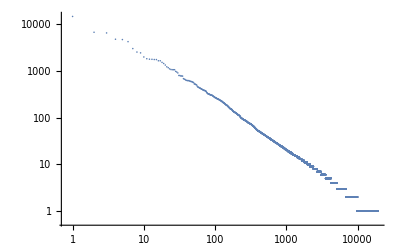

```mathematica
ListLogLogPlot[(Sort[Last/@Tally[words],Greater])[[1;;]]]
```

```mathematica
ListLogLogPlot[(Sort[Tally[words][[All,-1]],Greater])[[1;;]]]
```

```mathematica
Sort[Last/@Tally[words],Greater]
```

```mathematica
Tally[words]
```

```mathematica
Table[Flatten[Tally[words][[Position[Last/@Tally[words],Sort[Last/@Tally[words],Greater][[k]]]//Flatten]]],{k,1,10}]
```

```mathematica
Reverse@SortBy[Tally[words],Last]
```

{{the,14614},{of,6708},{and,6487},{a,4757},{to,4678},{in,4223},{that,3002},{his,2529},{it,2429},{i,1985},{but,1821},{he,1779},{with,1770},{as,1751},{is,1747},{for,1646},{was,1645},{all,1522},{this,1440},19177,{115,1},{114,1},{113,1},{112,1},{111,1},{110,1},{11,1},{109,1},{108,1},{107,1},{106,1},{105,1},{10,440,1},{104,1},{103,1},{102,1},{101,1},{100,1},{10,1}}
 |  |  |  |

```mathematica
Tally[words][[Flatten[Position[Tally[words],{"whale",_}]]]]
```

```mathematica
Select[Reverse@SortBy[Tally[words],Last],#[[1]]=="whale"&]
```

## Zipf’s Law in different languages

Here we compare texts in different languages with Zipf’s Law.

```mathematica
Manipulate[
{DTitle,DText,pts,FTable,LM,LT,UT}=GetText[DTextNr,TFTS];
If[R>UT,R=UT];
Grid[{
{Grid[{{Column[{
Text@Style[Pane[Grid[{{"term","rank","occ."}},Dividers->Center,Background->LightBrown,FrameStyle->Directive[White],Alignment->Center,ItemSize->{{8,3,3}}],ImageSize->{203,16}],Darker[Purple]],
Text@Style[
Pane[Grid[FTable,Frame->None,Dividers->Center,Alignment->Center,ItemSize->{{8,3,3}},Background->{None,{{LightYellow,LightBrown}}},FrameStyle->Directive[White]],ImageSize->{203,175},Scrollbars->{False,True},Alignment->{Top,Left}]
],Text@Style[Pane["total number of terms: "<>ToString[LT],ImageSize->{203,21},Alignment->{Center,Bottom}]],Text@Style[Pane["unique terms: "<>ToString[UT],ImageSize->{203,14},Alignment->{Center,Top}]]},Alignment->Center,Spacings->{Automatic,0}],Pane[Show[ListLogLogPlot[pts,AxesLabel->{Row[{"rank"}],"occurrences"},PlotRange->All,PlotStyle->Directive[ColorData["HTML","MediumVioletRed"],PointSize[Large]],
Epilog->Inset[Tooltip[Panel[Text@Column[{"best linear approximation:",Row[{Style["y",Italic]," = ",Normal[LM]/.x->Style["x",Italic]}],Row[{Superscript[Style["R",Italic],2], " = ",ToString[LM["RSquared"]]}]},Center],Appearance->Frameless],Column[{Row[{"coefficient of determination = ",Superscript[Style["R",Italic],2],ToString[LM["RSquared"]]}],LM["ParameterTable"]}]],Offset[{3,3},Scaled[{1,1}]],{Right,Top}]],Plot[LM[x],{x,0,R},PlotStyle->Directive[ColorData["HTML","Indigo"]]]],ImageSize->{360,240}]}},Spacings->{2,0}]},
{Pane[Row[{Pane[Text@Style[DText,Italic,12],ImageSize->{520,130},Scrollbars->{False,True}]},Background->ColorData["HTML","OldLace"]],Alignment->{Bottom,Center},ImageSize->{520,130}]}},Spacings->{0,1}]
,
{{DTextNr,7,"example text"},Dynamic[Table[i->GetTitle[i],{i,50}],SynchronousUpdating->False],PopupMenu},
{{TFTS,1,"sort term frequency table"},{1->"by frequency",2->"alphabetically"},ControlType->SetterBar},
{{UT,1,"number of unique terms"},ControlType->None},
{{R,100,Tooltip["up to rank","consider only terms up to this rank"]},1,UT,1,Appearance->"Labeled"},
ControlPlacement->Top,
SynchronousUpdating->False,
SynchronousInitialization->False,
TrackedSymbols->True,
AutorunSequencing->{2},
Initialization:>(
IndexedVariable[var_,{indicesValues__}]:=With[{dict=List[indicesValues]},Scan[(var[#[[1]]]=#[[2]])&,dict]];
DText="";
FTable={};
GetText[tn0_,tfts0_]:=Module[{tn=tn0,tfts=tfts0,tname,tterms,tcontent,uterms,title,findex,pts,ftable,lm,lt,ut},
tname=ToString[ExampleData["Text"][[tn]][[2]],OutputForm];
tcontent=ExampleData[{"Text",tname}];
tterms=If[Intersection[{ExampleData[{"Text",tname},"Language"]},{"Chinese","Greek","Hawaiian","Indonesian","Japanese","Korean","Maori","Russian","Swahili"}]=={},ToLowerCase /@StringSplit[tcontent,Except[WordCharacter]..],ExampleData[{"Text",tname},"Words"]];
lt=Length[tterms];
uterms=Flatten[Union[Table[{i},{i,tterms}]]];
ut=Length[uterms];
IndexedVariable[findex,Tally[tterms]];
ftable=Reverse[SortBy[Table[{t,findex[t]},{t,uterms}],Last]];
ftable=Table[{ftable[[i,1]],i,ftable[[i,2]]},{i,If[R≤ut,R,ut]}];
pts=Table[Tooltip[{i,ftable[[i]][[3]]},Column[{Text@Style[ftable[[i]][[1]],Italic,12],  Text@Style["rank = " <> ToString[i] <>  " occurrences = "  <> ToString[ ftable[[i]][[3]]],11]},Alignment->Center,Dividers->Center]],{i,If[R≤ut,R,ut]}];
ftable=Which[tfts==1,Reverse[SortBy[ftable,Last]],tfts==2,SortBy[ftable,First]];
lm=LinearModelFit[Map[Log,pts[[All,1]],{2}],{x},{x}];
title=GetTitle[tn];
{title,tcontent,pts,ftable,lm,lt,ut}
];
GetTitle=(StringReplace[StringReplace[ExampleData["Text"][[#]][[2]],x:CharacterRange["A","Z"]:>" "<>x]," "~~WordBoundary->"",1])&
)]
```

## Matrix Population Models

Matrix population models are commonly used to describe populations of individuals of different age classes.

```mathematica
ClearAll["Global`*"]
```

```mathematica
Subscript[n, 1][t_]:= Subscript[n, 1][t]=Subscript[F, 1] Subscript[n, 1][t-1]+Subscript[F, 2] Subscript[n, 2][t-1]+Subscript[F, 3] Subscript[n, 3][t-1];
Subscript[n, 2][t_]:=Subscript[n, 2][t]=Subscript[P, 1] Subscript[n, 1][t-1];
Subscript[n, 3][t_]:=Subscript[n, 3][t]=Subscript[P, 2] Subscript[n, 2][t-1];
```

```mathematica
Subscript[n, 1][0]=10.;Subscript[n, 2][0]=2.;Subscript[n, 3][0]=1.;Subscript[F, 1]=20.;Subscript[F, 2]=20.;Subscript[F, 3]=10.;Subscript[P, 1]=0.05;Subscript[P, 2]=0.1;
```

```mathematica
tcourse=Table[{Subscript[n, 1][t],Subscript[n, 2][t],Subscript[n, 3][t]},{t,0,10}];
```

```mathematica
tcourse
```

```mathematica
ListLogPlot[Transpose[tcourse]]
```

Again as in the earlier models the population grows exponentially. Let’s first write the system as a matrix-vector product:

```mathematica
ClearAll["Global`*"]
```

```mathematica
Subscript[F, 1]=20.;Subscript[F, 2]=20.;Subscript[F, 3]=10.;Subscript[P, 1]=0.05;Subscript[P, 2]=0.1;
```

```mathematica
A={{Subscript[F, 1],Subscript[F, 2],Subscript[F, 3]},{Subscript[P, 1],0,0},{0,Subscript[P, 2],0}};
```

```mathematica
{{Subscript[F, 1],Subscript[F, 2],Subscript[F, 3]},{Subscript[P, 1],0,0},{0,Subscript[P, 2],0}}//MatrixForm
```

The vector at time zero is

```mathematica
vpop={10.,2.,1.}
```

```mathematica
NestList[A.#&,vpop,5]
```

```mathematica
ListLogPlot[Transpose[%]]
```

If we want to know the percentages of individuals in the different age groups, we can proceed as with the random walk on the websites.

```mathematica
NestList[A.#/(Total[A.#])&,vpop/Total[vpop],7]
```

```mathematica
ListLogPlot[Transpose[%],Joined-> True]
```

Alternatively, we can determine the eigenvector to the largest eigenvalue of A:

```mathematica
Abs/@ Eigenvectors[A][[1]]
```

Let’s take another example:

```mathematica
A={{0,1,5},{0.3,0,0},{0,0.5,0}}
```

Let’s produce an adjacency graph for this matrix. First we take all non-zero entries to one:

```mathematica
A/.x_/;x>0->1
```

Now we can plot the graph:

```mathematica
AdjacencyGraph[Transpose[A/.x_/;x>0->1],VertexLabels->"Name",ImagePadding->30]
```

Initially we only have “young” individuals.

```mathematica
vpop={1,0,0}
```

```mathematica
tcourse=NestList[A.#/(Total[A.#])&,vpop/Total[vpop],50];
```

```mathematica
ListPlot[Transpose[tcourse],Joined-> True]
```

```mathematica
Eigenvectors[A][[1]]
```

We observe that there are initial fluctuations, but then the time series settles down to some constant values. What happens if the fertility and death rates change a bit?

```mathematica
ClearAll["Global`*"]
```

```mathematica
rand:=RandomVariate[NormalDistribution[0,0.05]]
```

```mathematica
A:={{0,1*(1+rand),5(1.+rand)},{0.3*(1+rand),0,0},{0,0.5*(1+rand),0}}
```

```mathematica
vpop={1,0,0}
```

```mathematica
tcourse=NestList[A.#/(Total[A.#])&,vpop/Total[vpop],50];
```

```mathematica
ListPlot[Transpose[tcourse],Joined-> True]
```

Let’s iterate for a bit longer.

```mathematica
tcourse=NestList[A.#/(Total[A.#])&,vpop/Total[vpop],200];
```

```mathematica
ListPlot[Transpose[tcourse],Joined-> True]
```

```mathematica
MatrixForm /@NestList[A.#&,A,30]
```

```mathematica
-1*Eigenvectors[#][[1]]&/@NestList[A.#&,A,30]
```

```mathematica
-1*Eigenvectors[#][[1]]&/@NestList[A.#&,A,30][[-10;;]]
```

```mathematica
Mean /@ Transpose[%]
```

```mathematica
results=Sign[Eigenvectors[#][[1,1]]]*Eigenvectors[#][[1]]&/@NestList[A.#&,A,10000][[30;;]];
```

```mathematica
Norm[results[[-10]]]
```

```mathematica
Show[Graphics3D[{Opacity[0.5],Sphere[{0,0,0}]}],ListPointPlot3D[results]]
```

For slightly different parameters the distribution becomes clearer.

```mathematica
rand:=RandomVariate[UniformDistribution[{0,1}]];
A:={{0,2*(1+rand),5(1.+rand)},{2.3*(1+rand),0,0},{0,1.5*(1+rand),0}}
vecs=Sign[Eigenvectors[#][[1,1]]]*Eigenvectors[#][[1]]&/@NestList[A.#&,A,10000][[30;;]];
```

The following command (slightly complicated) draws the distribution (the histogram) colour coded onto the surface of the sphere.

```mathematica
hist=Image[SmoothDensityHistogram[{ArcTan[#1,#2],ArcCos[#3]}&@@@vecs,AspectRatio->Automatic,ColorFunction->"ThermometerColors",Frame->False,ImagePadding->None,PerformanceGoal->"Quality",PlotRange->{{-π,π},{0,π}},PlotRangePadding->None],ImageResolution->256];
(*you can use SphericalPlot3D[] instead*)
ParametricPlot3D[{Cos[
θ] Sin[φ],Sin[θ] Sin[φ],Cos[φ]},{θ,-π,π},{φ,0,π},Lighting->"Neutral",Mesh->None,PlotStyle->Texture[hist],TextureCoordinateFunction->({#4,#5}&)]
```

It is certainly interesting to calculate that distribution analytically as it will help us to understand the fluctuations of the population. We will have a closer look at linear stochastic systems again very soon, when we discuss AutoRegressive Moving Average (ARMA) Processes.

```mathematica
ClearAll["Global`*"]
```

What if A is not a matrix but rather some general operator?

This was A:

```mathematica
A:={{0,1,5},{0.3,0,0},{0,0.5,0}};
```

Now we make it

```mathematica
A:={(3.94*#[[2]](1.-#[[2]])+4.0*#[[3]](1.-#[[3]]))/2,3.2*#[[1]]*(1.-#[[1]]),2.9*#[[2]](1.-#[[2]])}&
```

```mathematica
tcourse=Transpose[NestList[A,{RandomReal[],0,0},200]];
```

```mathematica
ListLinePlot[tcourse,AspectRatio->0.2,ImageSize->{1000,300}]
```

We should look at this for some longer time series and plot it in 3 dimensions.

```mathematica
tcourse=Transpose[NestList[A,{RandomReal[],0,0},50000]];
```

```mathematica
ListPointPlot3D[Transpose[tcourse],PlotStyle-> PointSize[Tiny]]
```

Let’s look at the distribution of these on the sphere:

```mathematica
vecs=(Normalize /@ NestList[A,{RandomReal[],0,0},10000])[[100;;]];
```

```mathematica
hist=Image[SmoothDensityHistogram[{ArcTan[#1,#2],ArcCos[#3]}&@@@vecs,AspectRatio->Automatic,ColorFunction->"ThermometerColors",Frame->False,ImagePadding->None,PerformanceGoal->"Quality",PlotRange->{{-π,π},{0,π}},PlotRangePadding->None],ImageResolution->256];
(*you can use SphericalPlot3D[] instead*)
ParametricPlot3D[{Cos[
θ] Sin[φ],Sin[θ] Sin[φ],Cos[φ]},{θ,-π,π},{φ,0,π},Lighting->"Neutral",Mesh->None,PlotStyle->Texture[hist],TextureCoordinateFunction->({#4,#5}&)]
```

These types of model can be applied for survival statistics, e.g. for life insurances.

## Probability/transition/stochastic matrices

When we have a transition matrix the idea is that we look at the percentages with which each “component” transits into other classes. Let’s take the matrix from the previous example.

```mathematica
A={{0,1,5},{0.3,0,0},{0,0.5,0}}
```

It had the following graph:

```mathematica
AdjacencyGraph[Transpose[A/.x_/;x>0->1],VertexLabels->"Name",ImagePadding->30]
```

To obtain the percentages we need to normalise each column to one.

```mathematica
atransition=Table[ A[[i]]/Total[A[[i]]],{i,1,Length[A]}]
```

Note that every column is now normalised so that the sum of its components is one. A fundamental theorem from algebra says that a probability matrix has a unique largest eigenvalue with magnitude one.

```mathematica
Eigenvalues[atransition]
```

As before the eigenvector corresponding to the largest eigenvalues describes the equilibrium distribution.

```mathematica
Eigenvectors[atransition][[1]]/Total[Eigenvectors[atransition][[1]]]
```

Transition matrices will become important in many models. We will encounter them again when we discuss evolutionary processes.

## Modelling Heat Transfer, from Newton to Fourier

```mathematica
ClearAll["Global`*"]
```

The problem of heat transfer has fascinated scientists for a long time. Newton described the cooling for an object. He used the simple assumption that the change of the temperature of an object is proportional to the temperature difference of the environment and the object.

```mathematica
(∂Temp(t))/(∂t)==-κ (Temp(t)-TU)
```

Here Temp is the temperature of the object and TU is the temperature of the environment, e.g. the ambient air. The coefficient κ indicates how fast the adaptation to the outside temperature takes place.

```mathematica
sols=DSolve[{D[Temp[t],t]==-κ(Temp[t]-TU),Temp[0]==T0},Temp,t]
```

{{Temp→Function[{t},ⅇ^(-t κ) (T0-TU+ⅇ^(t κ) TU)]}}

Here we assumed that the starting temperature is T0. If we assume the starting temperature to be 80°C and the air temperature to be 20°C, and κ=0.1 we obtain the following plot.

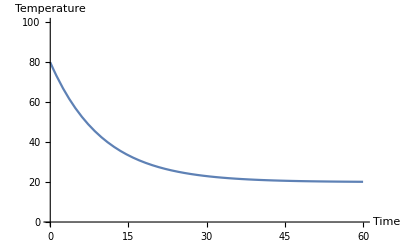

```mathematica
Plot[Temp[t]/.sols/. {κ-> 0.1,TU-> 20,T0-> 80},{t,0,60},PlotRange-> {All,{0,100}},AxesLabel->{"Time","Temperature"},LabelStyle->Directive[Bold, Medium]]
```

This shows how the object cools down.

We can now convert the function into discrete “measurements”

```mathematica
measurements=Table[{t,(Temp[t]-TU/.sols/. {κ-> 0.1,TU-> 20,T0-> 80})[[1]]},{t,0,60}];
```

```mathematica
ListLogPlot[measurements]
```

```mathematica
Fit[{#[[1]],Log[#[[2]]]}& /@measurements,{x,1},x]
```

The 0.1 is the numerical value of κ.

### In fact we can use a combination of Arduino and Mathematica to actually measure temperature with an external sensor.

We use the Arduino and wire it like so:

We then need to upload an Arduino C-program -actually some dialect-, which is called Sketch, to the microcontroller.

#include <OneWire.h>
#include <DallasTemperature.h>
 
// Data wire is plugged into pin 2 on the Arduino
#define ONE_WIRE_BUS 2
 
// Setup a oneWire instance to communicate with any OneWire devices 
// (not just Maxim/Dallas temperature ICs)
OneWire oneWire(ONE_WIRE_BUS);
 
// Pass our oneWire reference to Dallas Temperature.
DallasTemperature sensors(&oneWire);
 
void setup(void)
{
  // start serial port
  Serial.begin(9600);

  // Start up the library
  sensors.begin();
}
 
 
void loop(void)
{
 
  sensors.requestTemperatures(); // Send the command to get temperatures

  Serial.print(sensors.getTempCByIndex(0),4); 
  Serial.print(“,”);
}

This upload is done via the Arduino IDE

The Arduino is connected via a serial (i.e. USB) cable to the computer. Mathematica can connect to the serial port like so:

```mathematica
myDSTemperature=DeviceOpen["Serial",{Quiet[FileNames["tty.usb*",{"/dev"},Infinity]][[1]],"BaudRate"->9600}]
```

DeviceObject[…]

We can then run a ScheduledTask every second:

```mathematica
s={};tZero=AbsoluteTime[];DeviceReadBuffer[myDSTemperature];

RunScheduledTask[AppendTo[s,{AbsoluteTime[]-tZero,ToExpression@(StringSplit[FromCharacterCode@DeviceReadBuffer[myDSTemperature],","][[-1]])}],1]
```

ScheduledTaskObject[…]

We can then display the result:

```mathematica
Dynamic[ListLinePlot[s,PlotRange->{All, {20,40}}]]
```

When we are done we can finish the ScheduledTask:

```mathematica
RemoveScheduledTask/@ScheduledTasks[];
```

and then close the connection to the Arduino:

```mathematica
DeviceClose[myDSTemperature]
```

### Competition: UoA mug versus Bruce’s mug.

We did the measurement with two different mugs. First we load the data:

```mathematica
data=Import["~/Desktop/temperaturedataBrucevsUoA.csv"];
```

Then there is a bit of cleaning to do.

```mathematica
dataclean=Table[Join[{data[[k]][[1;;6]]},data[[k]][[7;;9]]],{k,1,Length[data]}];
```

This produces a list of dates/times and tempertures for mug 1 (“Bruce’s Mug”):

```mathematica
data2plotmug1=Select[Transpose[{dataclean[[All,1]],dataclean[[All,2]]/1000.}],#[[2]]>0&];
```

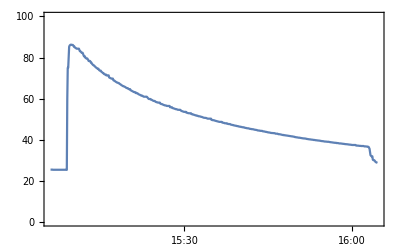

```mathematica
DateListPlot[data2plotmug1,PlotRange->{All,{0,100}}]
```

This is for mug 2 (“UoA mug”):

```mathematica
data2plotmug2=Select[Transpose[{dataclean[[All,1]],dataclean[[All,3]]/1000.}],#[[2]]>0&];
```

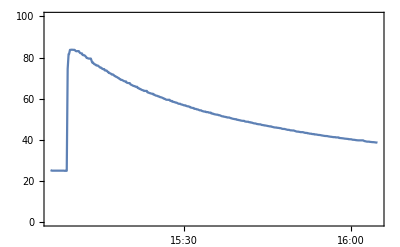

```mathematica
DateListPlot[data2plotmug2,PlotRange->{All,{0,100}}]
```

We also have a test temperature sensor; this is important to obtain the air temperature.

```mathematica
data2plotair=Select[Transpose[{dataclean[[All,1]],dataclean[[All,4]]/1000.}],#[[2]]>0&];
```

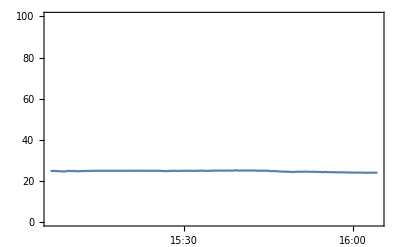

```mathematica
DateListPlot[data2plotair,PlotRange->{All,{0,100}}]
```

In order to calculate the cooling rate we need to find out when the measurements were taken. They were taken at approximately 5 seconds, but there were many false measurements which we needed to get rid of.

We prepare the data for the fitting:

```mathematica
{AbsoluteTime[#[[1]]]-AbsoluteTime[dataclean[[All,1]][[1]]],Log[#[[2]]]}& /@ data2plotmug1;
```

And then we “fit the first mug”:

```mathematica
Fit[{AbsoluteTime[#[[1]]]-AbsoluteTime[dataclean[[All,1]][[1]]],Log[#[[2]]]}& /@ data2plotmug1,{x,1},x]
```

4.17619-0.000163718 x

What about the second mug?

```mathematica
Fit[{AbsoluteTime[#[[1]]]-AbsoluteTime[dataclean[[All,1]][[1]]],Log[#[[2]]]}& /@ data2plotmug2,{x,1},x]
```

4.22706-0.000154572 x

Here comes the value in “per minute”.

```mathematica
Fit[{(AbsoluteTime[#[[1]]]-AbsoluteTime[dataclean[[All,1]][[1]]])/60.,Log[#[[2]]]}& /@ data2plotmug2,{x,1},x]
```

4.22706-0.00927433 x

## The eternal conundrum

Every morning I consume a caffeinated hot beverage with sugar and (more importantly for this problem) with milk. Just after pouring the delicious beverage into the mug it has a temperature of about 80 degrees. I usually add a good portion of standard, semi-skimmed milk, which we assume to be from the fridge ; 5 or so degrees. As it happens (nearly every morning) I am late, but do not want to be burnt by the smokingly hot liquid. So, when do I add the milk? As soon as possible or just before I really have to leave.

We already know that the cooling of the drink depends on its difference to the room temperature.

```mathematica
(∂Temp(t))/(∂t)==-κ (Temp(t)-TU)
```

Mixing of liquids (of the same kind, we assume Tcaffee > Tair > Tmilk), leads to this

```mathematica
Tmix=(mc Tc+mm Tm)/(mc+mm)
```

where Tmix is the temperature of the resulting coffee-milk mix, mc and mm are the mass of the coffee and the milk, and Tc and Tm their respective temperatures. First we put the milk in right at the beginning:

```mathematica
sols=NDSolve[{D[Temp[t],t]==-0.1(Temp[t]-20),Temp[0]==80,WhenEvent[t>1,Temp[t]-> (200. Temp[t]+50.* 5.)/250.]},Temp,{t,0,30}]
```

{{Temp→InterpolatingFunction[{{0., 30.}}, <>]}}

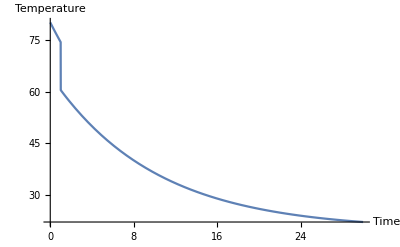

```mathematica
Plot[Temp[t] /. sols,{t,0,30},PlotRange-> All,AxesLabel->{"Time","Temperature"},LabelStyle->Directive[Bold, Medium]]
```

Next we wait for 10 minutes and then pour the milk in:

```mathematica
sols2=NDSolve[{D[Temp[t],t]==-0.1(Temp[t]-20),Temp[0]==80,WhenEvent[t>10,Temp[t]-> (200.* Temp[t]+50.* 5.)/250.]},Temp,{t,0,30}]
```

{{Temp→InterpolatingFunction[{{0., 30.}}, <>]}}

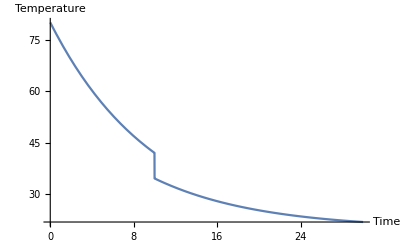

```mathematica
Plot[Temp[t] /. sols2,{t,0,30},PlotRange-> All,AxesLabel->{"Time","Temperature"},LabelStyle->Directive[Bold, Medium]]
```

When we plut both curves together we see that:

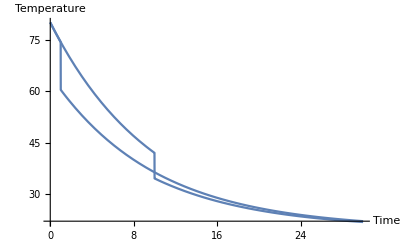

```mathematica
Show[Plot[Temp[t] /. sols,{t,0,30},PlotRange-> All],Plot[Temp[t] /. sols2,{t,0,30},PlotRange-> All],AxesLabel->{"Time","Temperature"},LabelStyle->Directive[Bold, Medium]]
```

The winner is: Pour the milk in as late as you can.

And here is the meaurement...

```mathematica
ClearAll["Global`*"]
```

```mathematica
data=Import["~/Desktop/temperaturedata_CoffeMilkGood.csv"];
```

```mathematica
dataclean=Table[Join[{data[[k]][[1;;6]]},data[[k]][[7;;9]]],{k,1,Length[data]}];
```

```mathematica
data2plotearlymilk=Select[Transpose[{dataclean[[All,1]],dataclean[[All,3]]/1000.}],#[[2]]>0&];
```

```mathematica
data2plotlatemilk=Select[Transpose[{dataclean[[All,1]],dataclean[[All,2]]/1000.}],#[[2]]>0&];
```

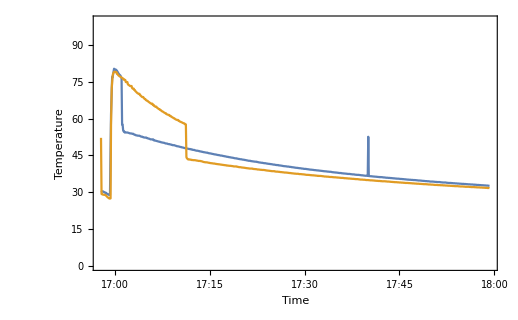

```mathematica
DateListPlot[{data2plotearlymilk,data2plotlatemilk},PlotRange->{All,{0,100}},Joined-> True,FrameLabel->{"Time","Temperature"},LabelStyle->Directive[Bold, Medium]]
```

## Cooling/Heating with changing ambient temperature

In our calculations so far we have ignored a potential change in the ambient temperature.

Let’s consider a periodically changing ambient temperature:

```mathematica
(∂Temp(t))/(∂t)==-κ (Temp(t)-TU (sin(t ω)+1))
```

This yields:

```mathematica
ClearAll["Global`*"]
```

```mathematica
sols=DSolve[{D[Temp[t],t]==-κ(Temp[t]-TU*(1+Sin[ω*t])),Temp[0]==80},Temp,t]
```

{{Temp→Function[{t},(ⅇ^(-t κ) (80 κ^2-TU κ^2+ⅇ^(t κ) TU κ^2+TU κ ω+80 ω^2-TU ω^2+ⅇ^(t κ) TU ω^2-ⅇ^(t κ) TU κ ω Cos[t ω]+ⅇ^(t κ) TU κ^2 Sin[t ω]))/(κ^2+ω^2)]}}

And then

```mathematica
Manipulate[Plot[Temp[t]/.sols/. {κ-> 0.1,TU-> 20, ω-> ω1},{t,0,200},PlotRange-> {All,{0,100}}],{{ω1,0},0,10}]
```

Of course, we can also model the case where the ambient temperature does not change so regularly, but rather eratically. We first create a “randomly perturbed” oscillating time series:

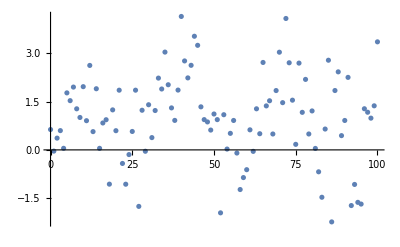

```mathematica
Table[{t,RandomVariate[NormalDistribution[]]+1+Sin[0.2*t]},{t,0,100}]//ListPlot
```

And then interpolate between the points:

```mathematica
tcourseTemp=Interpolation[Table[{t,RandomVariate[NormalDistribution[]]+1+Sin[0.2*t]},{t,0,100}]]
```

InterpolatingFunction[{{0., 100.}}, <>]

```mathematica
Plot[tcourseTemp[t],{t,0,100}]
```

We can now use that as external temperature into our model:

```mathematica
sols2=NDSolve[{D[Temp[t],t]==-κ(Temp[t]-TU*tcourseTemp[t]),Temp[0]==20.}/.{κ-> 0.4,TU-> 10.},Temp,{t,0,100}]
```

{{Temp→InterpolatingFunction[{{0., 100.}}, <>]}}

```mathematica
Plot[Temp[t]/.sols2,{t,0,100},PlotRange-> {All,All}]
```

This curve is much smoother (low pass filter!). Plotting both functions into one diagram gives:

```mathematica
Show[{Plot[10.*tcourseTemp[t],{t,0,100},PlotStyle-> Red,PlotRange-> All],Plot[Temp[t]/.sols2,{t,0,100},PlotRange-> {All,All}]}]
```

Such a model could be amended to describe the heat loss of a house, and help us to develop an optimal heating strategy.

## Model for the temperature of soil at different depths

When we want to describe the diffusion of heat into the soil we need to use a partial differential equation.

```mathematica
(∂θ(x,t))/(∂t)==κ (∂^2 θ(x,t))/(∂x^2)
```

We will model the influence of the surface heating by the boundary conditions.

```mathematica
ClearAll["Global`*"]
f[t]:= 10.+A Sin[ω t]/. {A-> 10.,ω-> 1./35.};sols=NDSolve[{D[θ[x,t],t]==0.05* D[θ[x,t],{x,2}],θ[0,t]==f[t],θ[x,0]==f[t]/.t-> 0,D[θ[x,t],x]==0/. x->0},θ[x,t],{x,0,10},{t,0.0,1200}]
```

This gives:

```mathematica
Plot3D[θ[x,t]/. sols,{x,0,10},{t,0,1200},PlotRange-> All]
```

We can clearly see the (annual/daily?) fluctuations and how the heat diffuses into the ground. A contour plot shows the temperature distribution in a clearer way:

```mathematica
ContourPlot[θ[x,t]/. sols,{x,0,9},{t,0,1200},PlotRange-> All,FrameLabel->{"Depth","Time"},LabelStyle->Directive[Medium,Bold]]
```

We observe that “at some depth there is winter in summer”. Let’s change a bit the timescales to make it more “realistic”.

```mathematica
ClearAll["Global`*"]
f[t]:= 10.+A Sin[ω t]/. {A-> 10.,ω-> 2.Pi/365.};sols=NDSolve[{D[θ[x,t],t]==0.01* D[θ[x,t],{x,2}],θ[0,t]==f[t],θ[x,0]==f[t]/.t-> 0,D[θ[x,t],x]==0/. x->0},θ[x,t],{x,0,10},{t,0.0,1200},PrecisionGoal->10]
```

```mathematica
ContourPlot[θ[x,t]/. sols,{x,0,10},{t,0,1200},PlotRange-> All,PlotLegends->True,Contours-> 20,FrameLabel->{"Depth","Time"},LabelStyle->Directive[Medium,Bold]]
```

We can now plot the temperature curves at different depths.

```mathematica
Plot[{θ[x,t]/. sols/. x-> 0,θ[x,t]/. sols/. x-> 1,θ[x,t]/. sols/. x-> 2,θ[x,t]/. sols/. x-> 3,θ[x,t]/. sols/. x-> 3.5},{t,0,1200},AxesLabel-> {"Time/[days]","Temperatre/[degrees Celsius]"},LabelStyle->Directive[Medium],ImageSize-> Large]
```

We observe a phase shift and a substantial damping of the amplitude at different depths. We can now also study what happens when we have daily and annual fluctuations of the temperature.

```mathematica
ClearAll["Global`*"]
f[t]:= 10.+A Sin[ω t]+B*Sin[2 Pi t]/. {A-> 10.,B-> 6.,ω-> 2.Pi/365.};sols=NDSolve[{D[θ[x,t],t]==0.01* D[θ[x,t],{x,2}],θ[0,t]==f[t],θ[x,0]==f[t]/.t-> 0,D[θ[x,t],x]==0/. x->0},θ[x,t],{x,0,10},{t,0.0,1200},PrecisionGoal->100,MaxSteps->Infinity,MaxStepFraction->1/1000.]
```

{{θ[x,t]→InterpolatingFunction[{{0., 10.}, {0., 1200.}}, <>][x,t]}}

```mathematica
ContourPlot[θ[x,t]/. sols,{x,0,2},{t,0,1200},PlotRange-> All,PlotLegends->True,Contours-> 20]
```

We see that the daily fluctuations only influence the very top layers of the soil. Only the longer oscillations penetrate the soil. Again we can plot a profile of the temperature fluctuations at different depths.

```mathematica
Plot[{θ[x,t]/. sols/. x-> 0,θ[x,t]/. sols/. x-> 0.02,θ[x,t]/. sols/. x-> 0.04,θ[x,t]/. sols/. x-> 0.06,θ[x,t]/. sols/. x-> 0.08},{t,0,20}]
```

## Soil temperature for Aberdeen

Based on the air temperature data for Aberdeen we can now model the expected temperature distribution in the soil (ignoring many factors...).

```mathematica
ClearAll["Global`*"]
```

First we need to get the temperature data for Aberdeen (actually the airport, EGPD) for a couple of years:

```mathematica
tempAberdeencity=WeatherData[LinguisticAssistant,"Temperature",{{2011, 1, 1},Date[], "Day"}]["Values"];
```

```mathematica
tempAberdeen=WeatherData["EGPD","Temperature",{{2011, 1, 1},Date[], "Day"}]["Values"];
```

As these are discrete points, we need to interpolate to obtain an input function for our model:

```mathematica
f=Interpolation[Transpose[{Range[Length[tempAberdeen]]-1,tempAberdeen}]]
```

InterpolatingFunction[…]

The resulting function looks like this:

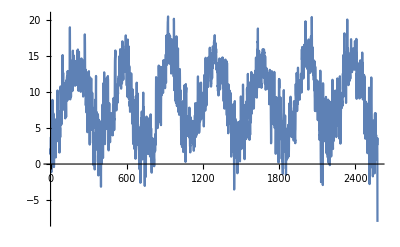

```mathematica
Plot[f[x],{x,0,Length[tempAberdeen]}]
```

We now feed that into our model and integrate:

```mathematica
f=Interpolation[Transpose[{Range[Length[tempAberdeen]]-1,tempAberdeen}]];sols=NDSolve[{D[θ[x,t],t]==0.01* D[θ[x,t],{x,2}],θ[0,t]==f[t],θ[x,0]==Mean[tempAberdeen],D[θ[x,t],x]==0/. x->0},θ[x,t],{x,0,10},{t,0,Length[tempAberdeen]-1},PrecisionGoal->100,MaxSteps->Infinity,MaxStepFraction->1/1000.]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

{{θ[x,t]→InterpolatingFunction[{{0., 10.}, {0., 2572.}}, <>][x,t]}}

```mathematica
(*no problems with the boundary conditions:
f=Interpolation[Transpose[{Range[Length[tempAberdeen]]-1,tempAberdeen}]];sols=NDSolve[{D[θ[x,t],t]==0.01* D[θ[x,t],{x,2}],θ[0,t]==f[t],θ[x,0]==f[0],D[θ[x,t],x]==0/. x->0},θ[x,t],{x,0,10},{t,0,Length[tempAberdeen]-1},PrecisionGoal->100,MaxSteps->Infinity,MaxStepFraction->1/1000.]*)
```

In this case we can ignore the warning. Plotting the solution gives:

```mathematica
ContourPlot[θ[x,t]/. sols,{x,0,5},{t,0,Length[tempAberdeen]},PlotRange-> All,PlotLegends->True,Contours-> 20,FrameLabel->{"Depth","Time"},LabelStyle->Directive[Medium,Bold],ColorFunction->"TemperatureMap"]
```

It is known how the amplitude of the temperature fluctuations changes at different depths.

We can reproduce that graph for our Aberdonian model:

```mathematica
tempdepth=Join[Table[{Mean[Table[θ[x,t]/. sols/.x-> g,{t,1,1000}]][[1]]+StandardDeviation[Table[θ[x,t]/. sols/.x-> g,{t,1,1000}]][[1]],-g},{g,0,5,0.05}],Table[{Mean[Table[θ[x,t]/. sols/.x-> g,{t,1,1000}]][[1]]+-StandardDeviation[Table[θ[x,t]/. sols/.x-> g,{t,1,1000}]][[1]],-g},{g,0,5,0.05}]];
```

```mathematica
(* remove average  
tempdepth=Join[Table[{StandardDeviation[Table[θ[x,t]/. sols/.x-> g,{t,1,1000}]][[1]],-g},{g,0,5,0.05}],Table[{-StandardDeviation[Table[θ[x,t]/. sols/.x-> g,{t,1,1000}]][[1]],-g},{g,0,5,0.05}]];*)
```

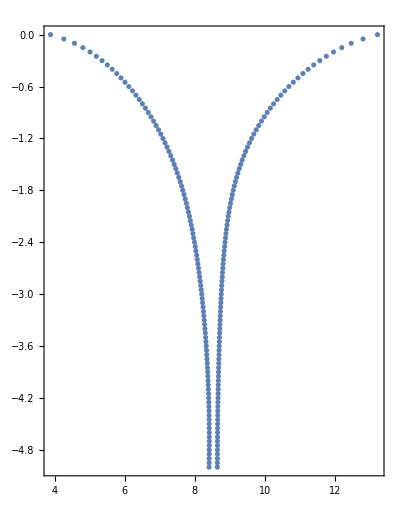

```mathematica
ListPlot[tempdepth,PlotRange->All,AspectRatio->1.3,Frame->{{False,True},{False,True}},FrameTicks-> All,FrameLabel-> {{"","Depth in Meters"},{"","Temperature in Celsius"}},LabelStyle->Directive[Medium,Bold]]
```

This one looks more like for Aberdeen.